# Analysis of Simulations of Retinal Mosaics

## Supplement for the “Unsupervised Learning of Cone Spectral Classes from Natural Images” (Benson NC, Manning JR, Brainard DH (2014) PLoS Comput. Biol. Submitted).

Copyright © 2013-2014 Noah C. Benson
Distributed under the Eclipse Public License.

## Introduction

### Constants/Parameters

```mathematica
Needs["ErrorBarPlots`"];
```

#### File System Parameters

```mathematica
$BaseDir=StringJoin[
If[ToLowerCase[$MachineName]=="seacucumber",
"/Users/nben",
"/Volumes/nben-1"],
"/Documents/ReceptorLearning"];
$DataDir=$BaseDir<>"/Code/Data/simulations-for-paper";
$MatlabSimDir=$DataDir<>"/matlab";
$ClojureSimDir=$DataDir<>"/java";
$MatlabSamplesSimDir=$MatlabSimDir<>"/vary-number-of-images/post-processed";
$ExportedDir=$BaseDir<>"/Code/exported_for_paper";
$FiguresDir=$BaseDir<>"/Paper/figures";
$NatImgDir=$BaseDir<>"/Code/Data/natural-image-statistics";
```

#### Setup keywords used in the datastructures of simulation data

```mathematica
Unprotect[RetinaKey];
ClearAll[RetinaKey];
RetinaKeyword::usage="RetinaKey[arg1, arg2, ...] declares all the given args as keywords in the receptor learning context (given by $RetinaContextName); each arg may be a symbol or a rule symbol->usage where usage is a string.";
RetinaKey[keys__]:=With[
{heldkeys=Hold/@Hold[keys]},
With[
{keysWithMsgs=Select[
heldkeys,
heldkey↦(Apply[Head,heldkey]===Rule)],
keysWithoutMsgs=Select[
heldkeys,
heldkey↦(Apply[Head,heldkey]=!=Rule)]},
Scan[
heldkey↦With[
{key=Map[Hold,heldkey,{2}][[1,1]],
msg=Map[Hold,heldkey,{2}][[1,2]]},
Unprotect@@key;
ClearAll@@key;
Evaluate[ReleaseHold[key]]::usage=ReleaseHold[msg];
Begin["`Private`"];
Set@@Join[key,key];
Protect@@key;
End[]],
keysWithMsgs];
Scan[
heldkey↦(
Unprotect@@heldkey;
ClearAll@@heldkey;
Set[
Evaluate[MessageName@@Join[heldkey,Hold[usage]]],
"This symbol is a keyword and will always evaluate to itself"];
Begin["`Private`"];
Set@@Join[heldkey,heldkey];
Protect@@heldkey;
End[]),
keysWithoutMsgs]]];
Protect[RetinaKey];
Attributes[RetinaKey]={HoldAll,Protected};
```

### Embedding Flattening Method

Flattens the simulation embedding using separate layers of gaussian fits.

```mathematica
Unprotect[FlattenEmbedding];
ClearAll[FlattenEmbedding];
FlattenEmbedding::usage="FlattenEmbedding[data] yields a flattened version of data, which must be a list of 3D points. This function assumes that data is to be flattened from layered curves along the first dimension. This is intended as a low-level function used by ClojureSim[]; generally you should access a simulation's flattened embedding via FlatEmbedding[sim].";
Begin["`Private`"];
FlattenEmbedding[dat_]:=Block[
{f,a0,ax,ay,axx,ayy,axy},
f[a0_Real,ax_Real,ay_Real,axx_Real,axy_Real,ayy_Real]:=StandardDeviation[
Map[
p↦Abs[
Subtract[
p[[1]],
(a0+ax*p[[2]]+ay*p[[3]]+axx*p[[2]]^2+axy*p[[2]]*p[[3]]+ayy*p[[3]]^2)]],
dat]];
With[
{sol=Quiet[
FindMinimum[
f[a0,ax,ay,axx,axy,ayy],
{a0,Mean[dat[[All,1]]]},
{ax,0.001},
{ay,0.001},
{axx,StandardDeviation[dat[[All,2]]]},
{axy,0},
{ayy,StandardDeviation[dat[[All,3]]]}],
{FindMinimum::lstol,
FindMinimum::cvmit,
FindMinimum::sdprec}]},
Map[
pt↦Prepend[
pt[[2;;3]],
pt[[1]]-(a0+ax*pt[[2]]+ay*pt[[3]]+axx*pt[[2]]^2+axy*pt[[2]]*pt[[3]]+ayy*pt[[3]]^2)/.sol[[2]]],
dat]]];
Attributes[FlattenEmbedding]={Protected};
End[];
```

### Clustering Method

```mathematica
RetinaKey[
SampleFunction->"SampleFunction is a sub-option to the NonlinearModelFit option of ClassifyLWSCones and ConeClasses. If this option is given, then it must be a function that accepts a smooth kernel distribution and yields a list of points at which it should be sampled for use in fitting the distribution model. The default (Automatic) uses the number of embedded points divided by 4.",
KernelBandwidth->"KernelBandwidth is a sub-option to the NonlinearModelFit option of ClassifyLWSCones and ConeClasses. If this option is given, then it must be a form that can be passed to SmoothKernelDistribution as its second argument. The default is 0.0002, though Automatic can be specified to use Mathematica's automatic choice.",
SmoothingKernel->"SmoothingKernel is a sub-option to the NonlinearModelFit option of ClassifyLWSCones and ConeClasses. If this option is given, then it must be a form that can be passed to SmoothKernelDistribution as its third argument. The default is \"Gaussian\".",
StartParameters->"StartParameters is a sub-option to the NonlinearModelFit and EstimatedDistribution option of ClassifyLWSCones and ConeClasses. If this option is given, then it must be a either a single list of three numbers {μ,σ,α} or a list of length 4 lists {{w[1],μ[1],σ[1],α[1]} ...} where w[i] is the weight and μ, σ, and α stand for the mean, standard deviation, and skewness of each of the skew normal distributions used in fitting the distribution of embedded z values. Alternately, a function that takes both the distribution and the set of sampled {x,pdf} pairs and yields such a list may be given. The default guesses these from k-means clusters.",
ClassCount->"ClassCount is an option to ClassifyLWSCones and ConeClasses, which can be an integer specifying the only model (with ClassCount distributions) to fit to the embeddings or can be a list of integers specifying alternate models. By default this is {1,2,3}, specifying that first a model with 1 cone type then with 2 cone types then with 3 cone types should be attempted, and the first of these to fit the embedding with a significance beneath the significance level will be accepted.",
SignificanceTest->"SignificanceTest is an option to ClassifyLWSCones and ConeClasses, which must be of a form acceptable for passing as the third argument of DistributionFitTest. If this is a list of two elements, then the first must be of this form and the second is passed to the DistributionFitTest's Method option. The default is \"KolmogorovSmirnov\"."];
```

```mathematica
Unprotect[ClassifyLWSCones];
ClearAll[ClassifyLWSCones];
ClassifyLWSCones::usage="ClassifyLWSCones[embedding] yields the predicted types (numbered 1-k) of each of the cones in the embedding in the order given by the embedding. This function should generally not be used, as ConeClasses[sim] will give a hashed version of this; however, the arguments for ConeClasses are identical and the options are detailed here:
  * ClassCount (default: {1,2,3}) can be an integer specifying the only model (with ClassCount distributions) to fit to the embeddings or can be a list of integers specifying alternate models.
  * Print (default: False) can be set to True to have the fitting routine print the fits as it goes.
  * Method (default: NonlinearModelFit) can be one of NonlinearModelFit, EstimatedDistribution, or FindClusters, specifying which method is used to fit the models. EstimatedDistribution uses maximum likelihood estimation but is quite slow. NonlinearModelFit fits the PDFs of the distributions to a sampled density function and is recommended. FindClusters uses density clustering.
   * The NonlinearModelFit method can be specified as {NonlinearModelFit, opts...} where opts may include SampleFunction, KernelBandwidth, SmoothingKernel, and StartParameters (each of which has its own usage documentation). Additionally, a Method option may be given, in which case it is passed directly to the NonlinearModelFit function.
  * SignificanceLevel (default: 0.01) can be set to any p-value level that is required for a fit to be rejected.
  * SignificanceTest (default: \"KolmogorovSmirnov\") specifies the third argument passed to DistributionFitTest when calculating significance of fits.
  * StepMonitor (default: None) specifies a function that should be called after every fit of a model; the arguments are the distribution that was found, the number of skew normal histograms it contains, and the p-value of the distribution.";
Begin["`Private`"];

(* First, we define the helper functions for the various methods *)

(* The FindClusters method is quite simple... *)
ClassifyLWSConesFindClusters[zs_,k_]:=If[k==1,
SkewNormalDistribution[Mean[zs],StandardDeviation[zs],Skewness[zs]],
With[
{clusts=FindClusters[
zs->Range[Length@zs],
k,
Method->{"Agglomerate","Linkage"->"Median"}]},
MixtureDistribution[
Map[cl↦Length[cl]/Length[zs],clusts],
Map[
cl↦With[{points=zs[[cl]]},
SkewNormalDistribution[
Mean[points],
StandardDeviation[points],
Skewness[points]]],
clusts]]]];

(* This function will estimate initial parameters using a quick k-means clustering algorithm *)
ClassifyLWSConesEstimateStartingParameters[zs_,k_]:=If[k==1,
{Mean[zs],StandardDeviation[zs],Skewness[zs]},
With[
{clusts=FindClusters[
zs->Range[Length@zs],
k,
Method->{"Optimize","Iterations"->5}]},
Map[
cl↦With[
{points=zs[[cl]]},
{Length[points]/Length[zs],Mean[points],StandardDeviation[points],Skewness[points]}],
clusts]]];

(* The EstimatedDistribution method is slightly more complex. For this method, we calculate some prep data *)
ClassifyLWSConesPrepEstimatedDistribution[embedding_,K_,opts_]:=With[
{start=With[
{r=FilterRules[opts,StartParameters]},
If[r=={},None,r[[1,2]]]]},
If[
Or[
start===None,
And[
Not[ListQ[K]],
ListQ[start],
MatchQ[start,{_?NumberQ,_?NumberQ,_?NumberQ}]],
And[
ListQ[start],
Length[start]==Length[K],
MatchQ[start,{{_?NumberQ,_?NumberQ,_?NumberQ,_?NumberQ}..}]]],
start,
Die["Improper StartParameters option; see ?ClassifyLWSCones and ?StartParameters."]]];
ClassifyLWSConesEstimatedDistribution[zs_,k_,start_]:=With[
{initialParams=If[start===None,ClassifyLWSConesEstimateStartingParameters[zs,k],start]},
Block[{w,μ,σ,α},
If[k==1,
EstimatedDistribution[
zs,
SkewNormalDistribution[μ,σ,α],
{{μ,initialParams[[1]]},
{σ,initialParams[[2]]},
{α,initialParams[[3]]}},
AccuracyGoal->6],
EstimatedDistribution[
zs,
MixtureDistribution[
Table[w[i],{i,1,k}],
Table[
SkewNormalDistribution[μ[i],σ[i],α[i]],
{i,1,k}]],
Flatten[
Table[
{{w[i],initialParams[[i,1]]},
{μ[i],initialParams[[i,2]]},
{σ[i],initialParams[[i,3]]},
{α[i],initialParams[[i,4]]}},
{i,1,k}],
1],
AccuracyGoal->6]]]];

(* The NonlinearModelFit method is probably the most complex. For this method, we calculate some prep data as well *)
ClassifyLWSConesPrepNonlinearModelFit[embedding_,K_,opts_]:=With[
{zs=embedding[[All,1]]},
With[
{start=With[
{r=FilterRules[opts,StartParameters]},
If[r=={},None,r[[1,2]]]],
sampleFn=With[
{r=FilterRules[opts,SampleFunction]},
If[r=={},
With[
{min=Min[zs],max=Max[zs]},
dist↦Range[min,max,(max-min)/(Length[zs]/4)]],
r[[1,2]]]],
kbw=With[
{r=FilterRules[opts,KernelBandwidth]},
If[r=={},0.0002,r[[1,2]]]],
smoothker=With[
{r=FilterRules[opts,SmoothingKernel]},
If[r=={},"Gaussian",r[[1,2]]]],
method=With[
{r=FilterRules[opts,Method]},
If[r=={},Automatic,r[[1,2]]]]},
{If[
Or[
start===None,
And[
Not[ListQ[K]],
ListQ[start],
MatchQ[start,{_?NumberQ,_?NumberQ,_?NumberQ}]],
And[
ListQ[start],
Length[start]==Length[K],
MatchQ[start,{{_?NumberQ,_?NumberQ,_?NumberQ,_?NumberQ}..}]]],
start,
Die["Improper StartParameters option; see ?ClassifyLWSCones and ?StartParameters."]],
With[
{smoothDist=SmoothKernelDistribution[zs,kbw,smoothker]},
With[
{sampleZs=sampleFn[smoothDist]},
Map[z↦{z,PDF[smoothDist,z]},sampleZs]]],
method}]];
ClassifyLWSConesNonlinearModelFit[zs_,k_,{start_,pointsToFit_,method_}]:=With[
{initialParams=If[start===None,ClassifyLWSConesEstimateStartingParameters[zs,k],start],
min=Min[zs],
max=Max[zs],
sqrt2pi=Sqrt[2.0*Pi]},
Block[{z,w,μ,σ,α},
With[
{model=If[k==1,
SkewNormalDistribution[μ,σ,α],
MixtureDistribution[
Table[w[i],{i,1,k}],
Table[
SkewNormalDistribution[μ[i],σ[i],α[i]],
{i,1,k}]]],
params=If[k==1,
MapThread[List,{{μ,σ,α},initialParams}],
Flatten[
Table[
{{w[i],initialParams[[i,1]]},
{μ[i],initialParams[[i,2]]},
{σ[i],initialParams[[i,3]]},
{α[i],initialParams[[i,4]]}},
{i,1,k}],
1]],
constraints=If[k==1,
And[σ>0,-5<α<5],
Apply[
And,
Join[
Table[w[i]>0.001,{i,1,k}],
Table[σ[i]>0,{i,1,k}],
Table[
w[i]*PDF[SkewNormalDistribution[μ[i],σ[i],α[i]],μ[i]]>w[i+1]*PDF[SkewNormalDistribution[μ[i+1],σ[i+1],α[i+1]],μ[i]],
{i,1,k-1}],
Table[
w[i+1]*PDF[SkewNormalDistribution[μ[i+1],σ[i+1],α[i+1]],μ[i+1]]>w[i]*PDF[SkewNormalDistribution[μ[i],σ[i],α[i]],μ[i+1]],
{i,1,k-1}]]]]},
(* We want to try unconstrained optimization first; it's faster and usually better... *)
With[
{fitModelUnc=Quiet@NonlinearModelFit[
pointsToFit,
PDF[model,z],
params,
z,
Method->"QuasiNewton",
AccuracyGoal->6]},
With[
{fitModel=If[
And[
Head[fitModelUnc]===FittedModel,
TrueQ[constraints/.fitModelUnc["BestFitParameters"]]],
fitModelUnc,
Quiet@NonlinearModelFit[
pointsToFit,
{PDF[model,z],constraints},
params,
z,
Method->method,
AccuracyGoal->6]]},
ReplaceAll[
model,
If[Head[fitModel]===FittedModel,
fitModel["BestFitParameters"],
Map[Apply[Rule,#]&,params]]]]]]]];

(* We also need a function that finds the labels from the distribution that is found *)
ClassifyLWSConesLabelFromDist[dist_,zs_]:=If[
Head[dist]===SkewNormalDistribution,Table[1,{Length[zs]}],
With[
{pdfs=With[
{ord=Ordering[dist[[2]],All,#1[[1]]<#2[[1]]&]},
MapThread[
{w,d}↦Function[{z},w*PDF[d,z]],
{dist[[1,ord]],dist[[2,ord]]}]]},
Map[
z↦First[Ordering[#[z]&/@pdfs,-1]],
zs]]];

(* Finally we have the function itself. *)
ClassifyLWSCones[embedding_,OptionsPattern[]]:=With[
{K=Replace[
OptionValue[ClassCount],
{k_Integer/;k>0:>{k},
ks:{_?(And[IntegerQ[#],#>0]&)..}:>ks,
Automatic->{1,2,3},
_:>Die["Improper ClassCount option; see ?ClassCount"]}],
pval=Replace[
OptionValue[SignificanceLevel],
{p_/;And[NumberQ[p],0<p<1]:>p,
_:>Die["Improper SignificanceLevel option; see ?ClassifyLWSCones"]}]},
With[
{methodFn=With[
{methodArg=OptionValue[Method]},
Switch[
If[ListQ[methodArg],First[methodArg],methodArg],
(* NonlinearModelFit requires some metadata be passed to it, so we calculate that now *)
NonlinearModelFit,With[
{prep=ClassifyLWSConesPrepNonlinearModelFit[
embedding,
K,
If[ListQ[methodArg],Rest@methodArg,{}]]},
{zs,k}↦ClassifyLWSConesNonlinearModelFit[zs,k,prep]],
FindClusters,ClassifyLWSConesFindClusters,
EstimatedDistribution,With[
{prep=ClassifyLWSConesPrepEstimatedDistribution[
embedding,
K,
If[ListQ[methodArg],Rest@methodArg,{}]]},
{zs,k}↦ClassifyLWSConesEstimatedDistribution[zs,k,prep]],
_,Die["Unrecognized Method argument; see ?ClassifyLWSCones"]]],
sigtestFn=Replace[
OptionValue[SignificanceTest],
{{s_String,m_}:>({zs,dist}↦DistributionFitTest[zs,dist,s,Method->m]),
s_String:>({zs,dist}↦DistributionFitTest[zs,dist,s])}],
zs=embedding[[All,1]],
stepmonFn=Replace[
OptionValue[StepMonitor],
{False->None}]},
With[
{foundDist=First[
Fold[
{previous,k}↦If[previous[[2]]>pval,
previous,
With[
{dist=methodFn[zs,k]},
With[
{p=sigtestFn[zs,dist]},
If[stepmonFn=!=None,stepmonFn[dist,k,p]];
If[p>previous[[2]],{dist,p},previous]]]],
{Null,0},
K]]},
ClassifyLWSConesLabelFromDist[foundDist,zs]]]];
Options[ClassifyLWSCones]={
ClassCount->{1,2,3},
StepMonitor->None,
Method->NonlinearModelFit,
SignificanceLevel->0.01,
SignificanceTest->"KolmogorovSmirnov"};
Attributes[ClassifyLWSCones]={Protected};
End[];
```

### Simulations and Machinery for Dealing with Simulations

#### Filesystem and Filename Metadata

These lists and functions deal with extracting the metadata about the simulation from the simulation filename. Assuming simulation files were run using the simulate-some-retinas function in clojure or using the main function interface (i.e., with lein run ...) OR if the simulation filenames were determined using the simulation-filename (in the brainardlab.nben.retina.util namespace), then these should work fine.

```mathematica
Unprotect[$ClojureSimFilenameParts];
ClearAll[$ClojureSimFilenameParts];
$ClojureSimFilenameParts::usage="$ClojureSimFilenameParts is a low-leve variable used by the machinery that declares clojure simulations. If you have an alternative method of naming your simulations or if you wish to add additional metadata to the simulation filenames, this variable should not be edited at its source (or unprotected and changed); rather, use the DeclareMetadata[] and RemoveMetadata[] functions.";
Begin["`Private`"];
$ClojureSimFilenameParts={};
Protect[$ClojureSimFilenameParts];
End[];
```

```mathematica
Unprotect[DeclareSimulationMetadata];
ClearAll[DeclareSimulationMetadata];
DeclareSimulationMetadata::usage="DeclareSimulationMetadata[dataKeyword, regexPattern, patternToDataExpr, dataToFilenameFn, defaultInDecl, defaultInFilename] inserts a new metadata type into the simulation parsing machinery. This allows simulation files with names that match the data type to be automatically understood by the analysis machinery.
The first four of the arguments are required while the last two are optional.
The dataKeyword is the keyword associated with this type of data in Mathematica (i.e., this is the name Mathematica knows the metadata category as); any simulation sim whose filename matches the regexPattern will be setup such that sim[dataKeyword] is equal to the value of the data matched from the pattern.
The regexPattern is a pattern that is expected to be between commas in the simulation filename details; i.e., simulations are expected to have the filename sim[*].bin where the * is a series of <variable>=<value> or <flag> strings separated by commas. This pattern should match one of these strings.
The patternToDataExpr should be an expression using the \"$1\" type tags (see the documantation on RegularExpression) which is combined with the regexPattern upon matching and should yield the representation of the given metadata category for Mathematica.
The dataToFilenameFn is used to turn a simulation declaration into a filename; it must be a function that takes a piece of data (i.e., anything that can be returned by the patternToDataExpr expression) and should yield the string that would represent this piece of data in a filename. It should always be the case that the regexPattern/patternToDataExpr and the dataToFilenameFn are symmetric in that the result of one should always be the other.
The defaultInDecl keyword indicates the value that this metadata category assumes when dataKeyword is not given in a simulation declaration; e.g. what should the value be when RetinaSimulation[] is called?
The defaultInFilename is the default to assume if the value is not listed in the filename. A good example of this is the Dichromat flag, which if not given is assumed to be False.";
Begin["`Private`"];
DeclareSimulationMetadata[tag_,regex_,inst_,rev_,decldef_]:=CompoundExpression[
Unprotect[$ClojureSimFilenameParts];
AppendTo[
$ClojureSimFilenameParts,
{tag,
RegularExpression[regex],
RuleDelayed[RegularExpression[regex],inst],
rev,
Hold[Die[ToString[tag]<>" not specified in filename!"]],
decldef}],
Protect[$ClojureSimFilenameParts]];
DeclareSimulationMetadata[tag_,regex_,inst_,rev_,decldef_,def_]:=CompoundExpression[
Unprotect[$ClojureSimFilenameParts];
AppendTo[
$ClojureSimFilenameParts,
{tag,
RegularExpression[regex],
RuleDelayed[RegularExpression[regex],inst],
rev,
Hold[def],
decldef}],
Protect[$ClojureSimFilenameParts]];
Attributes[DeclareSimulationMetadata]={HoldAll,Protected};
End[];
```

```mathematica
Unprotect[ClojureSimParameters];
ClearAll[ClojureSimParameters];
ClojureSimParameters::usage="ClojureSimParameters[] yields a list of all metadata parameters that may be passed to ClojureSim[] along with their default values; note that this does not list parameters such as Directory which do not specify simulation metadata.";
Begin["`Private`"];
ClojureSimParameters[]:=MapThread[Rule,Transpose[$ClojureSimFilenameParts[[All,{1,6}]]]];
End[];
```

```mathematica
Unprotect[ParseClojureSimFilename];
ClearAll[ParseClojureSimFilename];
ParseClojureSimFilename::usage="ParseClojureSimFilename[filename] yields a list of arguments suitable for the ClojureSim[] function; this is a low-level function that is not intended for general use; rather use the ClojureSim[] function itself.";
Begin["`Private`"];
ParseClojureSimFilename[flnm_String]:=Flatten[
StringCases[
flnm,
RuleDelayed[
RegularExpression[
"(.+)/sim\\[(.+)\\]\\.bin$"],
With[
{parts=StringSplit["$2",","],
dir="$1"},
Append[
MapThread[
Function[
With[{f=Flatten[#1]},
If[f=={},#2[[1]]->ReleaseHold[#2[[5]]],f]]],
{Outer[
Function[
If[StringMatchQ[#2,#1[[2]]],
#1[[1]]->First@StringCases[#2,#1[[3]]],
{}]],
$ClojureSimFilenameParts,
parts,
1,1],
$ClojureSimFilenameParts}],
Directory->dir]]]]];
Protect[ParseClojureSimFilename];
End[];
```

```mathematica
Unprotect[ClojureSimulationFileName];
ClearAll[ClojureSimulationFileName];
ClojureSimulationFileName::usage="ClojureSimulationFileName[...] reconstructs a filename from the given options, all of which must be either Directory or a match to a metadata category that has been declared with DeclareSimulationMetadata[]. This is a low-level function that is not indended for general use; instead use ClojureSim[].";
Begin["`Private`"];
ClojureSimulationFileName[opts__]:=With[
{parts=Map[
opt↦With[{tmp=FilterRules[{opts},opt[[1]]]},
If[tmp=={},opt[[4]][opt[[6]]],opt[[4]][tmp[[1,2]]]]],
$ClojureSimFilenameParts],
dir=With[{tmp=FilterRules[{opts},Directory]},
If[tmp=={},$ClojureSimDir,tmp[[1,2]]]]},
StringJoin[
If[dir===None,"",dir<>"/"],
"sim[",
Most@Flatten@Map[If[#===None,{""},{#,","}]&,Select[parts,StringQ]],
"].bin"]];
Attributes[ClojureSimulationFileName]={Protected};
End[];
```

```mathematica
Unprotect[ReadClojureSimFile];
ClearAll[ReadClojureSimFile];
ReadClojureSimFile::usage="ReadClojureSimFilename[filename] yields a list of the data contained in the clojure simulation file found at the given filename location. This is a low-level function that is not intended for general use; instead use ClojureSimp[].";
Begin["`Private`"];
ReadClojureSimFile[filename_String]:=Block[{$ByteOrdering=1},
With[
{f=OpenRead[filename,BinaryFormat->True]},
Check[
With[
{n=BinaryRead[f,"Integer32"]},
With[
{dat={
BinaryReadList[f,"Integer32",n],
Partition[BinaryReadList[f,"Real32",2*n],2],
Partition[BinaryReadList[f,"Real32",n*n],n]},
em=BinaryReadList[f,"Real32",3*n]},
Close[f];
If[em=={},
dat,
Append[dat,Transpose[Partition[em,n]]]]]],
(Close[f];$Failed)]]];
End[];
```

#### The metadata categories stored in clojure sim filenames

Here we declare the types of metadata we expect to find in the filenames of clojure simulations. See ?DeclareSimulationMetadata (which is also defined in the above section) for more information.

```mathematica
DeclareSimulationMetadata[
RetinaSize,
"mosaic=(r|h)(\\d+)x(\\d+)_([\\d\\.]+)",
With[
{tmp=(ToExpression/@{"$2","$3","$4"})},
If[tmp[[3]]==1.0&&tmp[[1]]==tmp[[2]],
tmp[[1]],tmp]],
Function[
StringJoin[
"mosaic=r",
If[ListQ[#],
StringJoin[
ToString[#[[1]]],"x",ToString[#[[2]]],
"_",
ToString[NumberForm[#[[3]],{3,1}]]],
ToString[#]<>"x"<>ToString[#]<>"_1.0"]]],
20];
```

```mathematica
DeclareSimulationMetadata[
Ls,
"L:M=(\\d+):(\\d+)",
With[
{tmp=(ToExpression/@{"$1","$2"})},
Round[94/Total[tmp]*tmp[[1]]]],
Function[
If[#==94,"L:M=1:0",
StringJoin[
"L:M=",
ToString[Max[{1,2^Round[Log[2,#/(94-#)]]}]],
":",
ToString[Max[{1,2^Round[Log[2,(94-#)/#]]}]]]]],
47];
```

```mathematica
DeclareSimulationMetadata[
MΛMax,
"Mlm=(\\d+|none)",
If["$1"=="none",None,ToExpression["$1"]],
("Mlm="<>If[#===None,"none",ToString[#]])&,
530];
```

```mathematica
DeclareSimulationMetadata[
Suppression,
"surround=(.+)",
If["$1"=="none",
0,
ToExpression/@StringSplit["$1","_"]],
Function[
StringJoin[
"surround=",
If[#===0,
"none",
ToString[#[[1]]]<>"_"<>ToString[NumberForm[#[[2]],{3,1}]]]]],
{0.25,3.0}];
```

```mathematica
DeclareSimulationMetadata[
Samples,
"samples=(\\d+)",
ToExpression["$1"],
("samples="<>ToString[#])&,
2000000,
2000000];
```

```mathematica
DeclareSimulationMetadata[
Tritanope,
"tritanope",
True,
If[#,"tritanope",None]&,
False,
False];
```

```mathematica
DeclareSimulationMetadata[
Run,
"run=(.+)",
With[{tmp="$1"},
With[{expr=ToExpression[tmp]},
If[NumberQ[expr],expr,tmp]]],
("run="<>ToString[#])&,
0];
```

```mathematica
DeclareSimulationMetadata[
Tetrachromat,
"tetrachromat=(\\d+)_(\\d+)",
{ToExpression["$1"],ToExpression["$2"]},
If[ListQ[#],
"tetrachromat="<>ToString[#[[1]]]<>"_"<>ToString[#[[2]]],
None]&,
False,
False];
```

```mathematica
DeclareSimulationMetadata[
Dichromat,
"dichromat",
True,
If[#,"dichromat",None]&,
False,
False];
```

#### The machinery necessary to declare a simulation and yield a tag to which all of its data is hashed.

These are most of the basic keywords found throughout this analysis file and particularly used here by the ClojureSim function when declaring and loading simulations. Other keywords are occasionally declared with the functions for which they are relevant.
For the most part, these keywords are either metadata tags (e.g., Meta[sim, RetinaSize] yields the retina size of sim) or tags to which values are hashed like functions (e.g., Index[sim] yields the index into the embedding for each of the cone classes). Keywords whose documentation mentions that they are meta keywords (usually with the string “(meta)”), are accessed as meta-data while others are treated much the same as functions. Generallt speaking, metadata is data that is obtained from the name of the simulation file.

```mathematica
RetinaKey[
RetinaSize->"RetinaSize is a keyword that represents the size of a retina (meta).",
Samples->"Samples is a keyword that represents the number of natural image patches shown to a retina simulation (meta).",
Suppression->"Suppression is a keyword that represents the surround suppression type of a retina simulation (meta).",
Ls->"Ls is a keyword that represents the number of L cones in a retina, usually as a percentage (meta).",
MΛMax->"MΛMax is a keyword that represents the λmax value of the M cones of a retina simulation (meta).",
Retina->"Retina is a keyword that represents the retina used in a simulation (meta).",
RawRetina->"RawRetina is a keyword that represents the height×width×classes matrix of a retina simulation in which, for all rows r and columns c, the list retina[[r,c]] is 0 at every cone class that the cone is not and 1 at the class of the cone (meta).",
Ratio->"Ratio is a keyword that represents the L:M ratio (or L:M:A ratio) of a retina simulation (meta).",
Embedding->"Embedding is a keyword that represents the full embedding of a simulation (meta).",
Tetrachromat->"Tetrachromat is a keyword that represents tetrachromatic retinas (meta).",
Dichromat->"Dichromat is a keyword that represents dichromatic retinas (meta).",
Tritanope->"Tritanope is a keyword that represents dichromatic retinas with L and M cones only (meta).",
LWS->"LWS is a keyword that represents the longer-wavelength-sensitive cones of a simulation only; LWS[sim] yields the indices (in the embedding) of the longer-wavelength-sensitive cones.",
LWSEmbedding->"LWSEmbedding is a keyword that represents the unflattened embedding of the longer-wavelength-sensitive cones (i.e., all but the S cones) of a simulation.",
FlatEmbedding->"FlatEmbedding is a keyword that represents the flattened embedding of the longer-wavelength-sensitive cones (i.e., all but the S cones) of a simulation.",
Index->"Index is a keyword that represents a list of the indices (e.g. in the embedding or the rows of the correlation matrix) of each cone of each class; the index itself is a list of lists, one per cone class, that contains the indices of each cone of the class. The lists should be sorted by inverse λmax.",
LWSIndex->"LWSIndex is a keyword that represents a list of the indices (e.g. in the LWS or flattened embedding) of each cone of each class except the S cones; the index itself is a list of lists, one per longer-wavelength-sensitive cone class, that contains the indices into the simulation's LWSEmbedding or FlatEmbedding of each cone of the class. The lists should be sorted by inverse λmax.",
FlatIndex->"FlatIndex is a keyword that serves as an alias for LWSIndex.",
TrueClasses->"TrueClasses is a keyword that represents a list of the (true) classes of the cones in the same order as LWSEmbedding lists them; this is also the order of the guesses returned from ConeClasses[sim].",
ConeClasses->"ConeClasses is a keyword that represents the types of the cones in a retina simulation, as determined by the clustering algorithm.",
FractionCorrect->"FractionCorrect is a keyword that represents the fraction of cones that were typed correctly by the algorithm; this is not the same as ConeScore.",
ClassificationScore->"ClassificationScore is a keyword that represents the average fraction of cones correctly classified over all longer-wavelength-sensitive cone classes in a retina simulation; this is not the same as FractionCorrect, which is the overall fraction independent of class.",
ClassesFound->"ClassesFound is a keyword that represents the number of cone classes identified by the clustering algorithm.",
L->"L is a keyword that represents L cones.",
M->"M is a keyword that represents M cones.",
S->"S is a keyword that represents S cones.",
A->"A is a keyword that represents anomalous (tetrachromatic) cones.",
CheckForFile->"CheckForFile is a keyword and option that may be passed to ClojureSim[] (default: True). If given as False, then no check will be made for the file; this is useful when the check might erroneously fail, such as when the file is in fact a URL beginning with http://.",
Meta->"Meta is a keyword that is used in the declaration of simulation options. Once a simulation has been declared using sim = ClojureSim[...], the options/metadata from the simulation filename will be available via Meta[sim, option], e.g., Meta[sim,RetinaSize].",
ClojureSimRawData->"ClojureSimRawData[sim] yields the raw simulation data for a declared clojure simulation (using ClojureSim[])."];
```

```mathematica
Unprotect[SimReadQ];
ClearAll[SimReadQ];
SimReadQ::usage="SimReadQ[sim] yields False if the clojure simulation sim has been declared but not been read; if sim is not a clojure simulation, yields Undefined. Otherwise, yields true. When a clojure simulation is declared using sim = ClojureSim[], ReadQ[sim] is False because the sim has been lazily declared; once it has been evaluated and read (by, for example, requesting Meta[sim,RetinaSize]), this becomes True.";
Begin["`Private`"];
SimReadQ[sim_]:=Undefined;
End[];
```

```mathematica
Unprotect[ClojureSimQ];
ClearAll[ClojureSimQ];
ClojureSimQ::usage="ClojureSimQ[sim] yields True if sim is a clojure simulation (declared by ClojureSim[]) and False otherwise.";
Begin["`Private`"];
ClojureSimQ[sim_]=False;
End[];
```

```mathematica
Unprotect[ClojureSim];
ClearAll[ClojureSim];
ClojureSim::usage="ClojureSim[...] declares a simulation with the parameters given in ...; these parameters may be examined via the ClojureSimParameters[] function. In addition to the metadata parameters given in ClojureSimParameters[], the following additional parameters may be given:
	*Directory (default: $ClojureSimDir) specifies the directory in which to find the simulation file.
	*CheckForFile (default: True) specifies whether a check should be made for the given file on declaration of the simulation.
	*Eigensystem (default: False) specifies, if true, that any embedding included in the simulation should be ignored, and instead the first three eigenvectors of the correlation matrix should be used.";
Begin["`Private`"];
ClojureSimOpts={
Directory->$ClojureSimDir,
Eigensystem->False,
CheckForFile->True};
ClojureSim[options__]:=With[
{opts=Flatten[{options}]},
With[
{flnm=ClojureSimulationFileName[options],
eigem=With[{o=FilterRules[opts,Eigensystem]},
If[o=={},False,Eigensystem/.First[o]]],
checkForFile=With[{o=FilterRules[opts,CheckForFile]},
If[o=={},True,CheckForFile/.First[o]]],
dat=Unique["sim"]},
dat/:File[dat]=flnm;
(* If this filename doesn't exist, we want to warn now... *)
If[checkForFile&&!FileExistsQ[flnm],
Print["Warning: File does not seem to exist for file \"",flnm,"\""]];
Scan[
opt↦TagSet[
dat,
Evaluate[Meta[dat,opt[[1]]]],
With[{tmp=FilterRules[opts,opt[[1]]]},
If[tmp=={},opt[[6]],tmp[[1,2]]]]],
$ClojureSimFilenameParts];
dat/:Meta[dat]:=TagSet[
dat,
Meta[dat],
Map[#->Meta[dat,#]&,$ClojureSimFilenameParts[[All,1]]]];
dat/:SimReadQ[dat]=False;
dat/:ClojureSimQ[dat]=True;
(* Here we lazily declare the simulation raw data... *) 
dat/:ClojureSimRawData[dat]:=TagSet[
dat,
ClojureSimRawData[dat],
With[
{raw=ReadClojureSimFile[File[dat]]},
If[raw===$Failed,Die["Could not load file: ",File[dat]]];
dat/:SimReadQ[dat]=True;
raw]];
(* Now we can define other aspects in terms of this... *)
dat/:RawRetina[dat]:=TagSet[
dat,
RawRetina[dat],
With[
{simdat=ClojureSimRawData[dat]},
If[Length[Meta[dat,RetinaSize]]==3,
Transpose[
Normal[
SparseArray[
MapThread[
(Append[Round[(#2-1)/Meta[dat,RetinaSize][[3]]+1],#1+1]->1)&,
simdat[[1;;2]]],
Round/@{
(Max[simdat[[2,All,1]]]-1)/Meta[dat,RetinaSize][[3]]+1,
(Max[simdat[[2,All,2]]]-1)/Meta[dat,RetinaSize][[3]]+1,
Max[simdat[[1]]]+1},
0]]],
Transpose[
Normal[
SparseArray[
MapThread[
(Append[Round[#2],#1+1]->1)&,
simdat[[1;;2]]],
Round/@{
Max@simdat[[2,All,1]],
Max@simdat[[2,All,2]],
Max[simdat[[1]]]+1},
0]]]]]];
dat/:Retina[dat]:=TagSet[
dat,
Retina[dat],
Map[
Last[Ordering[#]]&,
RawRetina[dat],
{2}]];
dat/:Correlation[dat]:=TagSet[
dat,
Correlation[dat],
ClojureSimRawData[dat][[3]]];
dat/:Index[dat]:=TagSet[
dat,
Index[dat],
Map[
Flatten[Position[Flatten[Retina[dat]],#]]&,
Union[Flatten[Retina[dat]]]]];
dat/:Embedding[dat]:=TagSet[
dat,
Embedding[dat],
With[{simdat=ClojureSimRawData[dat]},
(* Note that in the case of tritanopes, this will rotate such that L and M cones are maximally separated along the first dimension instead of LM/S cones. *)
With[
{em=If[Length@simdat==4&&Not[eigem],
simdat[[4]],
Transpose[Rest[Eigensystem[simdat[[3]],4][[2]]]]],
lm=Flatten[Most[Index[dat]]],
s=Last[Index[dat]]},
If[Meta[dat,Tritanope],
With[
{R=If[Mean[em[[lm,3]]]<Mean[em[[s,3]]],
RotationMatrix[{{0,0,-1},{-1,0,0}}],
RotationMatrix[{{0,0,-1},{1,0,0}}]]},
Map[Dot[R,#]&,em]],
With[
{R=RotationMatrix[
{Mean[em[[s]]]-Mean[em[[lm]]],
{1,0,0}}]},
Map[Dot[R,#]&,em]]]]]];
dat/:LWS[dat]:=TagSet[
dat,
LWS[dat],
If[Meta[dat,Tritanope],
Range[Length[Embedding[dat]]],
Sort[Flatten[Most[Index[dat]]]]]];
dat/:LWSEmbedding[dat]:=TagSet[
dat,
LWSEmbedding[dat],
With[
{em=Embedding[dat]},
Map[
idcs↦em[[idcs]],
LWS[dat]]]];
dat/:FlatEmbedding[dat]:=TagSet[
dat,
FlatEmbedding[dat],
FlattenEmbedding[LWSEmbedding[dat]]];
dat/:LWSIndex[dat]:=TagSet[
dat,
LWSIndex[dat],
With[
{key=Thread[
Evaluate[
Rule[
Sort[
Apply[
Join,
If[Meta[dat,Tritanope],Index[dat],Most[Index[dat]]]]],
Range[
Total[
Map[
Length,
If[Meta[dat,Tritanope],Index[dat],Most[Index[dat]]]]]]]]]},
Table[
ReplaceAll[Index[dat][[k]],key],
{k,1,If[Meta[dat,Tritanope],Length[Index[dat]],Length[Index[dat]]-1]}]]];
dat/:FlatIndex[dat]:=LWSIndex[dat];
dat/:TrueClasses[dat]:=TagSet[
dat,
TrueClasses[dat],
Part[
SortBy[
Flatten[
MapIndexed[
{id,pos}↦{id,pos[[1]]},
LWSIndex[dat],
{2}],
1],
First],
All,2]];
(* These are the clustering and clustering-related tags *)
dat/:ConeClasses[dat,args__]:=TagSet[
dat,
ConeClasses[dat,args],
With[
{classes=If[args===Null,
ClassifyLWSCones[FlatEmbedding[dat]],
ClassifyLWSCones[FlatEmbedding[dat],args]]},
(* In the case of tetrachromats there's a risk that the retina was defined as L,M,A,S or as L,A,M,S; we check both in this case only and take the better one *)
If[Meta[dat,Tetrachromat]=!=False,
With[
{alt=classes/.{2->3,3->2},
truth=TrueClasses[dat]},
With[
{sc=Total[MapThread[Boole[#1==#2]&,{truth,classes}]]/Length[truth],
altsc=Total[MapThread[Boole[#1==#2]&,{truth,alt}]]/Length[truth]},
If[sc>altsc,classes,alt]]],
classes]]];
dat/:ConeClasses[dat]:=TagSet[
dat,
ConeClasses[dat],
ConeClasses[dat,Null]];
dat/:ClassesFound[dat]:=TagSet[
dat,
ClassesFound[dat],
Length[Union[ConeClasses[dat]]]];
dat/:ClassesFound[dat,args__]:=TagSet[
dat,
ClassesFound[dat,args],
Length[Union[ConeClasses[dat,args]]]];
dat/:FractionCorrect[dat,args__]:=TagSet[
dat,
FractionCorrect[dat,args],
With[
{guess=If[args===Null,ConeClasses[dat],ConeClasses[dat,args]],
truth=TrueClasses[dat]},
Total[MapThread[Boole[#1==#2]&,{truth,guess}]]/Length[truth]]];
dat/:FractionCorrect[dat]:=FractionCorrect[dat,Null];
dat/:ClassificationScore[dat,args__]:=TagSet[
dat,
ClassificationScore[dat,args],
With[
{counts=Fold[
{sofar,next}↦With[
{correct=sofar[[1]],
total=sofar[[2]],
trueClass=next[[1]],
guess=next[[2]]},
{If[trueClass==guess,
ReplacePart[correct,trueClass->(correct[[trueClass]]+1)],
correct],
ReplacePart[total,trueClass->(total[[trueClass]]+1)]}],
Table[0,{2},{Length[FlatIndex[dat]]}],
Transpose[
{TrueClasses[dat],
If[args===Null,ConeClasses[dat],ConeClasses[dat,args]]}]]},
Mean[counts[[1]]/counts[[2]]]]];
dat/:ClassificationScore[dat]:=ClassificationScore[dat,Null];
(* All that is left to do is yield the symbol! *)
dat]];
Attributes[ClojureSim]={Protected};
End[];
```

These are some very simply but handy functions that are basically indistinguishable from the Tagged functions made by ClojreSim[].

```mathematica
Unprotect[LogLM];
ClearAll[LogLM];
LogLM::usage="LogLM[sim] yields the base-2 log of the L:M ratio rounded to an integer.";
Begin["`Private`"];
LogLM[sim_/;ClojureSimQ[sim]]:=Round[Log[2,Meta[sim,Ls]/(94-Meta[sim,Ls])]];
End[];
```

### Declaring Simulations

These code blocks all declare different sets of simulations. It should be relatively easy to add new simulation sets to this section.

#### Standard and basic simulations

Standard simulations are simulations (run=0) for 5x5, 10x10, 15x15, and 20x20 simulations, run with and without surround, for L:M rations from 1:16 to 16:1 and for M lambda max of 530 through 555. The subset of these that are 20x20 retinas with surround are also considered part of the basic set.

```mathematica
standardSims:=Set[
standardSims,
Map[
flnm↦ClojureSim[ParseClojureSimFilename[flnm]],
FileNames[$ClojureSimDir<>"/standard/*.bin"]]];
```

Basic simulations are simulations for 20x20 retinas with surround suppression, for L:M ratios from 1:16 to 16:1 and for M lambda max of 530 through 55 nm. These include run 0 of some of the standard sims (those that match the requirements) as well as runs 1 and 2 of the basic sims.

```mathematica
basicSims:=Set[
basicSims,
Join[
Map[
flnm↦ClojureSim[ParseClojureSimFilename[flnm]],
FileNames[$ClojureSimDir<>"/basic/*.bin"]],
Select[
standardSims,
sim↦Meta[sim,Suppression]=!=0&&Meta[sim,RetinaSize]==20]]];
```

#### Simulations run without manmade images

These simulations were run after natural images were scubbed from the hyperspectral cache; they represent a version of our simulation in which obviously manmade things were not shown to the retinas.

```mathematica
naturalSims:=Set[
naturalSims,
Map[
flnm↦ClojureSim[ParseClojureSimFilename[flnm]],
FileNames[$ClojureSimDir<>"/without-manmade/*.bin"]]];
```

#### Simulations of dichromats and tetrachromats

These simulations are of dichromats and tetrachromats.

```mathematica
nontrichromatSims:=Set[
nontrichromatSims,
Join[
Map[
flnm↦ClojureSim[ParseClojureSimFilename[flnm]],
FileNames[$ClojureSimDir<>"/ditetra/*.bin"]],
Map[
flnm↦ClojureSim[ParseClojureSimFilename[flnm]],
FileNames[$ClojureSimDir<>"/tritanopes/*.bin"]]]];
```

Tritanopes lack S cones but have L and M cones.

```mathematica
tritanopeSims:=Set[
tritanopeSims,
Select[
nontrichromatSims,
sim↦TrueQ[Meta[sim,Tritanope]]]];
```

Dichromats do not include tritanopes by convention; tetrachromats are unique in their own way and contain an extra datum, which is a list of {the ratio of anomalous cones, the anomalous cone lambda-max}.

```mathematica
dichromatSims:=Set[
dichromatSims,
Select[
nontrichromatSims,
sim↦TrueQ[Meta[sim,Dichromat]]]];
```

```mathematica
tetrachromatSims:=Set[
tetrachromatSims,
Select[
nontrichromatSims,
sim↦ListQ[Meta[sim,Tetrachromat]]]];
```

#### Simulations with blur incorporated into the hyperspectral cache

```mathematica
blurSims:=Set[
blurSims,
Map[
flnm↦ClojureSim[ParseClojureSimFilename[flnm]],
FileNames[$ClojureSimDir<>"/blur/*.bin"]]];
```

#### Simulations of nonhuman tetrachromat retinas with lambda-max values spaced evenly across the S->L range

```mathematica
nonhumanSims:=Set[
nonhumanSims,
Map[
flnm↦ClojureSim[ParseClojureSimFilename[flnm]],
FileNames[$ClojureSimDir<>"/spacing/*.bin"]]];
```

#### Simulations of the periphery

```mathematica
peripherySims:=Set[
peripherySims,
Map[
flnm↦ClojureSim[ParseClojureSimFilename[flnm]],
FileNames[$ClojureSimDir<>"/periphery/*.bin"]]];
```

#### Simulations with noise added

```mathematica
noise1Sims:=Set[
noise1Sims,
Map[
flnm↦ClojureSim[ParseClojureSimFilename[flnm]],
FileNames[$ClojureSimDir<>"/noise1/*.bin"]]];
```

```mathematica
noise5Sims:=Set[
noise5Sims,
Map[
flnm↦ClojureSim[ParseClojureSimFilename[flnm]],
FileNames[$ClojureSimDir<>"/noise5/*.bin"]]];
```

#### Simulations with cone-class-specific surround suppression

```mathematica
opponentSims:=Set[
opponentSims,
Map[
flnm↦ClojureSim[ParseClojureSimFilename[flnm]],
FileNames[$ClojureSimDir<>"/opponent/*.bin"]]];
```

#### Simulations run with various numbers of images

```mathematica
samplesSims:=Set[
samplesSims,
Map[
flnm↦ClojureSim[ParseClojureSimFilename[flnm]],
FileNames[$ClojureSimDir<>"/samples/*.bin"]]];
```

### Miscellaneous

#### Aesthetic Parameters

This list hash is used to determine the color for plotting the cones:

```mathematica
Unprotect[ConeColor];
ClearAll[ConeColor];
ConeColor::usage="ConeColor[coneKey] yields the color used when plotting the given coneKey, which must be L, M, A, or S.";
Begin["`Private`"];
ConeColor[L]:=Red;
ConeColor[M]:=Darker[Green];
ConeColor[A]:=Orange;
ConeColor[S]:=Blue;
ConeColor[_]:=Black;
Protect[ConeColor];
End[];
```

This yields a list of cone colors for a given simulation, based on the parameters of that simulation.

```mathematica
Unprotect[ConeColors];
ClearAll[ConeColors];
ConeColors::usage="ConeColors[simulation] yields a list of colors for each cone type in the given simulation, ordered from the cones sensitive to the longest wavelength to the cones sensitive to the shortest wavelength.";
Begin["`Private`"];
ConeColors[sim_]:=With[{n=Length[Index[sim]]},
Switch[n,
0,{},
1,{ConeColor[L]},
2,{ConeColor[L],ConeColor[S]},
3,ConeColor/@{L,M,S},
4,ConeColor/@{L,M,A,S},
_,Table[Hue[2.0/3.0*((k-1)/(n-1))],{k,1,n}]]];
Protect[ConeColors];
End[];
```

#### A Step status plotter for ClassifyLWSCones and ConeClasses

```mathematica
Unprotect[StepPlotter];
ClearAll[StepPlotter];
StepPlotter::usage="StepPlotter[sim] yields a function that is appropriate to be used as an argument to the StepMonitor option of ClassifyLWSCones and/or ConeClasses. It accepts the options KernelBandwidth and SmoothingKernel, which ideally should be identical to whatever versions of these options was passed to ClassifyLWSCones (these are used for making a smooth histogram of the data).";
Begin["`Private`"];
Options[StepPlotter]={
KernelBandwidth->Automatic,
SmoothingKernel->"Gaussian"};
StepPlotter[sim_,OptionsPattern[]]:=With[
{zs=FlatEmbedding[sim][[All,1]]},
With[
{min=Min[zs],
max=Max[zs]},
With[
{sh=SmoothHistogram[
FlatEmbedding[sim][[All,1]],
{OptionValue[KernelBandwidth],OptionValue[SmoothingKernel]},
PlotRange->{{min,max},Full},
Filling->Axis,
FillingStyle->LightGray,
BaseStyle->Directive[10,FontFamily->"Arial"],
Axes->None,
Frame->{{True,False},{True,False}},
FrameLabel->{{"Probability Density",None},{"z",None}},
PlotStyle->{{Black,Thick,Dashed}},
ImageSize->{3.25,2.15}*72]},
Function[{dist,k,p},
Print[
Graphics[
{Inset[
Show[
{sh,
Plot[
PDF[dist,z],
{z,min-(max-min),max+(max-min)},
PlotStyle->{{Thick,Darker@Green}},
PlotRange->Full]}],
ImageScaled[{0,0.5}],
ImageScaled[{0,0.5}]],
Text[
Style[
NumberForm[p,{5,5},NumberFormat->Function["p = "<>#1<>"E"<>#3]],
FontFamily->"Arial",
FontSize->10],
ImageScaled[{0.98,0.98}],
ImageScaled[{1,1}]],
Text[
Style[
MatrixForm[
If[k>1,
Prepend[
Table[
Prepend[List@@dist[[2,i]],dist[[1,i]]],
{i,1,k}],
{"w","μ","σ","α"}],
{{"μ","σ","α"},List@@dist}]],
FontFamily->"Arial",
FontSize->10],
ImageScaled[{0.75,0.5}],
ImageScaled[{0.5,1}]]},
ImageSize->{7,2.25}*72,
ImagePadding->2000]]]]]];
Protect[StepPlotter];
End[];
```

#### Error handling

This function lets us abort a calculation with an error message immediately.

```mathematica
Die[msg__]:=(Print[msg];Abort[]);
```

### Figure Plotting

#### Full Sized Plots

```mathematica
RetinaKey[
SeparateLegend->"SeparateLabel is an option to AccuracyPlot and related functions which specifies that the legend and the image should be rendered separately and returned as a list of {figure, legend} instead of being inset into a single graphics object.",
Simulations->"Simulations is an option to AccuracyPlot and related functions that must give the matrix of simulations from which the matrix being plotted was derived. These simulations will then be used to label the axes of the plot."]
```

```mathematica
Unprotect[AccuracyPlot];
ClearAll[AccuracyPlot];
AccuracyPlot::usage="AccuracyPlot[matrix] yields an ArrayPlot of the given matrix, which must contain numbers between 0 and 1. See the Figure 4 and Supplemental Figure 5 sections to see examples of how this function is generally used. The following options may be given:
  * SeparateLabel (default: False) may be set to True to indicate that instead of returning a composed graphic, the fucntion should yield a list of the {plot-graphic, label-graphic}.
  * Simulations (default: None) if given uses the matrix of simulations, from which the matrix to plot is assumed to be derived, to label the axes.
  * ColorFunction (default: Automatic) if given use the argument as the color function; otherwise use grayscale.";
Begin["`Private`"];
Options[AccuracyPlot]={
ColorFunction->Automatic,
SeparateLegend->False,
Simulations->None};
AccuracyPlot[dat_,OptionsPattern[]]:=With[
{colorf=Replace[
OptionValue[ColorFunction],
Automatic->Function[{val},
Which[
val==-1,Hue[2/3,1,0.4],
val<0,Red,
val>1,White,
val<0.5,Black,
True,Blend[{Black,White},(val-0.5)/0.5]]]],
simLabels=Replace[
OptionValue[Simulations],
{l_List/;Dimensions[l]==Dimensions[dat]:>l,
None->None,
_:>Die["Simulations and data matrix must have the same dimensions."]}],
separateLabels=Replace[
OptionValue[SeparateLegend],
Except[True|False]:>Die["SeparateLabels must be True or False."]]},
With[
{plot=ArrayPlot[
dat,
DataReversed->True,
ColorFunctionScaling->False,
ColorFunction->colorf,
BaseStyle->Directive[10,FontFamily->"Arial"],
FrameLabel->{
{"\!\(\*SubscriptBox[\(log\), \(2\)]\)(L:M)",None},
{If[Length@dat<2,None,"M cone \!\(\*SubscriptBox[\(λ\),\(max\)]\)"],None}},
FrameTicks->If[simLabels===None,
{{Thread[{Range[6],Range[530,555,5]}],False},
{Thread[{Range[9],Range[-4,4]}],False}},
{{Table[
{k,Meta[simLabels[[k,1]],MΛMax]},
{k,1,Length@simLabels}],
False},
{Table[
{k,LogLM[simLabels[[1,k]]]},
{k,1,Length@simLabels[[1]]}],
False}}],
ImageSize->{(3.25-0.85),2.05}*72],
legend=With[
{scale=Reverse[Table[{k,k},{k,0.5,1,0.02}]]},
ArrayPlot[
scale,
ColorFunction->colorf,
ColorFunctionScaling->False,
BaseStyle->Directive[10,FontFamily->"Arial"],
FrameTicks->{
{False,
Map[
{Position[scale[[All,1]],#][[1,1]],ToString[#]}&,
Range[0.5,1.0,0.1]]/.("1."->"1.0")},
{False,False}},
AspectRatio->5,
ImageSize->{0.85,1.2}*72]]},
If[separateLabels,
{plot,legend},
Graphics[
{Inset[
plot,
Scaled[{0,0.5}],
Scaled[{0.55,0.4}]],
Inset[
legend,
Scaled[{1,0.5}],
Scaled[{-0.5,0.4}]]},
ImageSize->{3.25,2.05}*72]]]];
Attributes[AccuracyPlot]={Protected};
End[];
```

```mathematica
Unprotect[ClustersPlot];
ClearAll[ClustersPlot];
ClustersPlot::usage="ClustersPlot[matrix] yields an ArrayPlot of the given matrix, which must contain non-negative integers. See the Figure 4 and Supplemental Figure 5 sections to see examples of how this function is generally used. The following options may be given:
  * SeparateLabel (default: False) may be set to True to indicate that instead of returning a composed graphic, the fucntion should yield a list of the {plot-graphic, label-graphic}.
  * Simulations (default: None) if given uses the matrix of simulations, from which the matrix to plot is assumed to be derived, to label the axes.
  * ColorFunction (default: Automatic) if given use the argument as the color function; otherwise use grayscale.
  * Range (default Automatic) specifies the range of possibilities to include on the legend; this may result in truncation of plot data in the case where the range excludes values in the matrix. This should be formatted as {min, max}. If Automatic, uses the min and max of the matrix.";
Begin["`Private`"];
Options[ClustersPlot]={
ColorFunction->Automatic,
SeparateLegend->False,
Simulations->None,
Range->Automatic};
ClustersPlot[dat_,OptionsPattern[]]:=With[
{colorf=Replace[
OptionValue[ColorFunction],
Automatic->Function[{val},Blend[{Black,White},val]]],
simLabels=Replace[
OptionValue[Simulations],
{l_List/;Dimensions[l]==Dimensions[dat]:>l,
None->None,
_:>Die["Simulations and data matrix must have the same dimensions."]}],
separateLabels=Replace[
OptionValue[SeparateLegend],
Except[True|False]:>Die["SeparateLabels must be True or False."]],
range=Replace[
OptionValue[Range],
{Automatic:>{Min[Flatten[dat]],Max[Flatten[dat]]},
l_List/;(Length[l]==2&&IntegerQ[l[[1]]]&&IntegerQ[l[[2]]]&&l[[1]]≥0&&l[[2]]>l[[1]]):>l,
_:>Die["Improper Range argument to ClusterPlot; see ?ClustersPlot for more information."]}]},
If[Length[Position[dat,x_Integer/;x≥0,{2}]]≠Length[Flatten[dat]],
Die["Data matrix must be a matrix of non-negative integers."]];
With[
{plot=ArrayPlot[
dat,
DataReversed->True,
ColorFunctionScaling->False,
ColorFunction->Function[{val},
colorf[
Which[
val>range[[2]],range[[2]],
val<range[[1]],range[[1]],
True,(val-range[[1]])/(range[[2]]-range[[1]])]]],
BaseStyle->Directive[10,FontFamily->"Arial"],
FrameLabel->{
{"\!\(\*SubscriptBox[\(log\), \(2\)]\)(L:M)",None},
{If[Length@dat<2,None,"M cone \!\(\*SubscriptBox[\(λ\),\(max\)]\)"],None}},
FrameTicks->If[simLabels===None,
{{Thread[{Range[6],Range[530,555,5]}],False},
{Thread[{Range[9],Range[-4,4]}],False}},
{{Table[
{k,Meta[simLabels[[k,1]],MΛMax]},
{k,1,Length@simLabels}],
False},
{Table[
{k,LogLM[simLabels[[1,k]]]},
{k,1,Length@simLabels[[1]]}],
False}}],
ImageSize->{(3.25-0.85),2.05}*72],
legend=Module[
{scale=Table[{k,k},{k,range[[1]],range[[2]]}]},
ArrayPlot[
Reverse@scale,
ColorFunction->Function[{val},colorf[(val-range[[1]])/(range[[2]]-range[[1]])]],
ColorFunctionScaling->False,
DataReversed->False,
DataRange->{{0,1},range},
BaseStyle->Directive[10,FontFamily->"Arial"],
FrameTicks->{{False,True},{False,False}},
AspectRatio->5,
ImageSize->{0.85,1.2}*72]]},
If[separateLabels,
{plot,legend},
Graphics[
{Inset[
plot,
Scaled[{0,0.5}],
Scaled[{0.55,0.4}]],
Inset[
legend,
Scaled[{1,0.5}],
Scaled[{-0.5,0.4}]]},
ImageSize->{3.25,2.05}*72]]]];
Protect[ClustersPlot];
End[];
```

#### Small Plots

```mathematica
Unprotect[SmallAccuracyPlot];
ClearAll[SmallAccuracyPlot];
SmallAccuracyPlot::usage="SmallAccuracyPlot[matrix] is identical to AccuracyPlot[matrix] except that it produces a smaller form of the plot more suitable for inclusion in a single-column figure (see ?AccuracyPlot for more information).";
Begin["`Private`"];
Options[SmallAccuracyPlot]={
ColorFunction->Automatic,
SeparateLegend->False,
Simulations->None};
With[{width=1.875,ar=0.7},
SmallAccuracyPlot[dat_,OptionsPattern[]]:=With[
{colorf=Replace[
OptionValue[ColorFunction],
Automatic->Function[{val},
Which[
val==-1,Hue[2/3,1,0.4],
val<0,Red,
val>1,White,
val<0.5,Black,
True,Blend[{Black,White},(val-0.5)/0.5]]]],
simLabels=Replace[
OptionValue[Simulations],
{l_List/;Dimensions[l]==Dimensions[dat]:>l,
None->None,
_:>Die["Simulations and data matrix must have the same dimensions."]}],
separateLabels=Replace[
OptionValue[SeparateLegend],
Except[True|False]:>Die["SeparateLabels must be True or False."]]},
With[
{plot=ArrayPlot[
dat,
DataReversed->True,
ColorFunctionScaling->False,
ColorFunction->colorf,
BaseStyle->Directive[10,FontFamily->"Arial"],
FrameLabel->{
{"\!\(\*SubscriptBox[\(log\), \(2\)]\)(L:M)",None},
{If[Length@dat<2,None,"M cone \!\(\*SubscriptBox[\(λ\),\(max\)]\)"],None}},
FrameTicks->If[simLabels===None,
{{Thread[{Range[6],Range[530,555,5]}],False},
{Thread[{Range[9],Range[-4,4]}],False}},
{{Table[
{Length[simLabels]+1-k,Meta[simLabels[[k,1]],MΛMax]},
{k,1,Length@simLabels}],
False},
{Table[
{k,LogLM[simLabels[[1,k]]]},
{k,1,Length@simLabels[[1]]}],
False}}],
ImageSize->width*72,
AspectRatio->ar],
legend=With[
{scale=Table[{k,k},{k,0.5,1,0.02}]},
ArrayPlot[
Transpose@scale,
ColorFunction->colorf,
ColorFunctionScaling->False,
BaseStyle->Directive[8,FontFamily->"Arial"],
FrameTicks->{
{False,False},
{Map[
{Position[scale[[All,1]],#][[1,1]],ToString[#]}&,
Range[0.5,1.0,0.1]]/.("1."->"1.0"),
False}},
AspectRatio->0.1,
ImageSize->1.3*72]]},
If[separateLabels,
{plot,legend},
Graphics[
{Inset[
legend,
ImageScaled[{0.625,1}],
ImageScaled[{0.5,1}]],
Inset[
plot,
ImageScaled[{0,0}],
ImageScaled[{0,0}]]},
ImageSize->{width,width*ar+0.425}*72,
ImagePadding->2000]]]]];
Protect[SmallAccuracyPlot];
End[];
```

```mathematica
Unprotect[SmallClustersPlot];
ClearAll[SmallClustersPlot];
SmallClustersPlot::usage="SmallClustersPlot[matrix] is identical to ClustersPlot[matrix] except that it produces a smaller form of the plot more suitable for inclusion in a single-column figure (see ?ClustersPlot for more information).";
Begin["`Private`"];
Options[SmallClustersPlot]={
ColorFunction->Automatic,
SeparateLegend->False,
Simulations->None,
Range->Automatic};
With[{width=1.875,ar=0.7},
SmallClustersPlot[dat_,OptionsPattern[]]:=With[
{colorf=Replace[
OptionValue[ColorFunction],
Automatic->Function[{val},Blend[{Black,White},val]]],
simLabels=Replace[
OptionValue[Simulations],
{l_List/;Dimensions[l]==Dimensions[dat]:>l,
None->None,
_:>Die["Simulations and data matrix must have the same dimensions."]}],
separateLabels=Replace[
OptionValue[SeparateLegend],
Except[True|False]:>Die["SeparateLabels must be True or False."]],
range=Replace[
OptionValue[Range],
{Automatic:>{Min[Flatten[dat]],Max[Flatten[dat]]},
l_List/;(Length[l]==2&&IntegerQ[l[[1]]]&&IntegerQ[l[[2]]]&&l[[1]]≥0&&l[[2]]>l[[1]]):>l,
_:>Die["Improper Range argument to ClusterPlot; see ?ClustersPlot for more information."]}]},
With[
{plot=ArrayPlot[
dat,
DataReversed->True,
ColorFunctionScaling->False,
ColorFunction->Function[{val},
colorf[
Which[
val>range[[2]],range[[2]],
val<range[[1]],range[[1]],
True,(val-range[[1]])/(range[[2]]-range[[1]])]]],
BaseStyle->Directive[10,FontFamily->"Arial"],
FrameLabel->{
{"\!\(\*SubscriptBox[\(log\), \(2\)]\)(L:M)",None},
{If[Length@dat<2,None,"M cone \!\(\*SubscriptBox[\(λ\),\(max\)]\)"],None}},
FrameTicks->If[simLabels===None,
{{Thread[{Range[6],Range[530,555,5]}],False},
{Thread[{Range[9],Range[-4,4]}],False}},
{{Table[
{Length[simLabels]+1-k,Meta[simLabels[[k,1]],MΛMax]},
{k,1,Length@simLabels}],
False},
{Table[
{k,LogLM[simLabels[[1,k]]]},
{k,1,Length@simLabels[[1]]}],
False}}],
ImageSize->width*72,
AspectRatio->ar],
legend=With[
{scale=Reverse[Transpose[Table[{k,k},{k,range[[1]],range[[2]]}]]]},
ArrayPlot[
scale,
ColorFunction->Function[{val},colorf[(val-range[[1]])/(range[[2]]-range[[1]])]],
ColorFunctionScaling->False,
BaseStyle->Directive[8,FontFamily->"Arial"],
FrameTicks->{{False,False},{True,False}},
DataRange->{range,{0,1}},
AspectRatio->0.1,
ImageSize->1.3*72]]},
If[separateLabels,
{plot,legend},
Graphics[
{Inset[
legend,
ImageScaled[{0.625,1}],
ImageScaled[{0.5,1}]],
Inset[
plot,
ImageScaled[{0,0}],
ImageScaled[{0,0}]]},
ImageSize->{width,width*ar+0.425}*72,
ImagePadding->2000]]]]];
Protect[SmallClustersPlot];
End[];
```

#### 3D Plots and Exporting Routines

Makes 3D plots of the embeddings (mostly for use with ExportRotatingImage)

```mathematica
Unprotect[SpherePlot3D];
ClearAll[SpherePlot3D];
SpherePlot3D::usage="SpherePlot3D[data] produces a 3D ";
Begin["`Private`"];
Options[SpheresPlot3D]={
PointSize->0.01,
PlotStyle->{ConeColor[L],ConeColor[M],ConeColor[S]},
ImageSize->3.25*72,
ViewAngle->Automatic,
ViewVertical->{0,0,1},
ViewCenter->Automatic,
ViewRange->All,
BoxRatios->Automatic,
Boxed->False,
ViewPoint->{1.3,-2.4,2.0}};
With[
{GraphicsInstructions=Function[{dat,sphereSize,style},
If[MatchQ[Dimensions[dat],{_,3}],
Prepend[
Map[
Sphere[#,sphereSize]&,
dat],
style],
Die["Data is not of 3D points"]]]},
SpheresPlot3D[dat_,OptionsPattern[]]:=Module[
{spheresz=Replace[OptionValue[PointSize],{x_}:>x],
styles=Replace[OptionValue[PlotStyle],{x_}:>x],
imsz=OptionValue[ImageSize],
dims=Dimensions[dat],
instr},
instr=If[MatchQ[dims,{_,3}],
GraphicsInstructions[dat,spheresz,styles],
MapIndexed[
Function[{pts,k},
GraphicsInstructions[
pts,
If[ListQ[spheresz],spheresz[[Mod[k[[1]],Length@spheresz]]],spheresz],
If[ListQ[styles],styles[[Mod[k[[1]]-1,Length@styles]+1]],styles]]],
dat]];
Graphics3D[
instr,
ImageSize->imsz,
ViewAngle->OptionValue[ViewAngle],
ViewVertical->OptionValue[ViewVertical],
ViewCenter->OptionValue[ViewCenter],
ViewRange->OptionValue[ViewRange],
ViewPoint->OptionValue[ViewPoint],
BoxRatios->OptionValue[BoxRatios],
Boxed->OptionValue[Boxed]]]];
Protect[SpherePlot3D];
End[];
```

```mathematica
Unprotect[Rotating3DEmbedding];
ClearAll[Rotating3DEmbedding];
Rotating3DEmbedding::usage="Rotating3DEmbedding[sim,type] takes identical parameters as SimpleEmbeddingPlot, but produces a list of images that, when viewed in sequence (or exported as a GIF, ideally with a DisplayDuration of 0.15), appears as a rotating embedding.";
Begin["`Private`"];
Rotating3DEmbedding[sim_,type:(LWS|Full|Flat)]:=With[
{em=Switch[type,
Full,Embedding[sim][[#]]&/@Index[sim],
LWS,LWSEmbedding[sim][[#]]&/@LWSIndex[sim],
Flat,FlatEmbedding[sim][[#]]&/@FlatIndex[sim]]},
With[
{μ=Mean/@Transpose[Flatten[em,1]],
r=4},
Table[
With[
{s=Mod[t,1]},
Image[
SpheresPlot3D[
em,
PointSize->0.005,
ViewPoint->If[t<1,
r*{Cos[s*2*Pi],Sin[s*2*Pi],0},
r*{Cos[s*2*Pi],0,Sin[s*2*Pi]}],
ViewCenter->{0.5,0.5,0.5},
ViewAngle->Pi/10,
ViewVertical->If[t<1,
{0,0,1},
{Cos[(s+0.02)*2*Pi],0,Sin[(s+0.02)*2*Pi]}-{Cos[s*2*Pi],0,Sin[s*2*Pi]}]]]],
{t,0,1.99,0.02}]]];
Protect[Rotating3DEmbedding];
End[];
```

#### Utilities

```mathematica
Unprotect[SimpleEmbeddingPlot];
ClearAll[SimpleEmbeddingPlot];
SimpleEmbeddingPlot::usage="SimpleEmbeddingPlot[sim,type] yields a simple 3D plot of the embedding of sim; type may be Full (for the full embedding), LWS (for all but the S cones), or Flat (for the flattened LWS comes). By default, type is Full.";
Begin["`Private`"];
SimpleEmbeddingPlot[sim_,type:(Full|Flat|LWS)]:=ListPointPlot3D[
Switch[type,
Full,Embedding[sim][[#]]&/@Index[sim],
LWS,LWSEmbedding[sim][[#]]&/@LWSIndex[sim],
Flat,FlatEmbedding[sim][[#]]&/@FlatIndex[sim]],
PlotStyle->ConeColors[sim],
BoxRatios->{1,1,1},
AxesLabel->{"X","Y","Z"},
BaseStyle->Directive[10,FontFamily->"Arial"]];
SimpleEmbeddingPlot[sim_]:=SimpleEmbeddingPlot[sim,Full];
Protect[SimpleEmbeddingPlot];
End[];
```

```mathematica
Unprotect[SimpleRetinaPlot];
ClearAll[SimpleRetinaPlot];
SimpleRetinaPlot::usage="SimpleRetinaPlot[sim] yields a small graphic of the retina of sim.";
Begin["`Private`"];
SimpleRetinaPlot[sim_]:=With[
{colors=ConeColors[sim],
r=Scaled[0.48/Length[Retina[sim]]]},
Graphics[
MapIndexed[
Function[{val,idx},
{colors[[val]],Disk[idx,r]}],
Retina[sim],
{2}],
ImageSize->0.9*72,
ImagePadding->2,
AspectRatio->1]];
Protect[SimpleRetinaPlot];
End[];
```

```mathematica
Unprotect[ExportFigure];
ClearAll[ExportFigure];
ExportFigure::usage="ExportFigure[name,figure] exports the figure to the filename name in the figures directory. A PDF and high-resolution TIFF are exported by default.";
Begin["`Private`"];
Options[ExportFigure]={
Format->{
{"PNG",ImageResolution->600},
{"TIFF",ImageResolution->600}},
Directory:>$FiguresDir};
ExportFigure[name_,figure_,OptionsPattern[]]:=With[
{flstart=OptionValue[Directory]<>"/"<>name<>"."},
Map[
format↦With[
{type=If[ListQ[format],First@format,format],
opts=If[ListQ[format],Rest@format,{}]},
Apply[
Export,
Join[
{flstart<>ToLowerCase[type],
figure,
ToUpperCase[type]},
opts]]],
Replace[
OptionValue[Format],
x_/;Not[ListQ[x]]:>{x}]]];
Protect[ExportFigure];
End[];
```

## Figures

### Figure 1: Natural Image Statistics

#### Load Data

For this figure, we load part A, which is an image from the Harvard Chakrabarti and Zickler (2011) hyperspectral image databasse that we have rendered into an RGB PNG representation using the clojure source code provided with this notebook. The function used to render the image was (save-hyperspectral-as-png ...). We lighten this image as well.

```mathematica
fig1`partA=Lighter[
Image[
Import[
"~/Temp/Chakrabarti2011/img032.png"],
ImageSize->1.25*72],
1.0];
fig1`natdat=Part[
SplitBy[
SortBy[
Import[$NatImgDir<>"/results.dat"],
#[[{2,1}]]&],
#[[2]]&],
All,All,{1,3}];
```

#### Generate Figure

```mathematica
fig1`figure=With[
{lbl=Function[{txt,coord,clr,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->Bold,
FontColor->clr],
Scaled[coord],
{0,0}]],
natdat=fig1`natdat,
x=Union[
Flatten[
Module[{tmp=N@Table[Range[0,19],{20}]},
Sqrt[tmp^2+Transpose[tmp]^2]]]],
maxchanneldiff=28},
Graphics[
{Inset[fig1`partA,ImageScaled[{0,1}],ImageScaled[{0,1}]],
Inset[
ListPlot[
natdat,
Joined->True,
Axes->None,
Frame->{{True,False},{True,False}},
FrameLabel->None,
BaseStyle->Directive[10,FontFamily->"Arial"],
PlotRange->{Full,{0.4,1}},
PlotStyle->Table[
{Thin,(*Hue[2/3*(1-k/(maxchanneldiff-1))]*)
Blend[{Black,Red,Yellow},k/(maxchanneldiff-1)]},
{k,0,maxchanneldiff-1}],
ImageSize->1.3*72,
AspectRatio->0.65],
ImageScaled[{0.48,1}],
ImageScaled[{0,1}]],
Inset[
Graphics[
{Text[
Style["Correlation",FontFamily->"Arial",FontSize->10],
{0,0},{0,0},{0,1}]}],
ImageScaled[{0.455,0.6}],
ImageScaled[{0.5,0.5}]],
Inset[
Style["Distance (pixels)",FontFamily->"Arial",FontSize->10],
ImageScaled[{0.705,0}],
ImageScaled[{0.5,0}]],
Inset[
ArrayPlot[
Table[{k,k,k,k},{k,0,(maxchanneldiff-1)*10}],
ColorFunction->(Blend[{Black,Red,Yellow},1-#/320]&),(*(Hue[2/3*(#/320)]&),*)
ColorFunctionScaling->False,
DataReversed->False,
BaseStyle->Directive[8,FontFamily->"Arial"],
ImageSize->{0.65,1}*72,
AspectRatio->12.5,
DataRange->{{0,1},{0,(maxchanneldiff-1)*10}},
FrameTicks->{{False,True},{False,False}},
PlotLabel->Style["Δλ (nm)",FontFamily->"Arial",FontSize->8]],
ImageScaled[{1,0.5}],
ImageScaled[{1,0.5}]],
Inset[
Style["(A)",FontFamily->"Arial",FontSize->10,FontWeight->Bold,FontColor->White],
ImageScaled[{0,1}],
ImageScaled[{0,1}]],
Inset[
Style["(B)",FontFamily->"Arial",FontSize->10,FontWeight->Bold],
ImageScaled[{0.41,1}],
ImageScaled[{0.4,1}]]},
ImagePadding->2000,
ImageSize->{3.25,1.1}*72]]
```

-Graphics-

#### Export

```mathematica
ExportFigure["fignatimg",fig1`figure];
```

### Figure 2: Retina, Spectral Sensitivities, and Correlations

#### Load/Prep Data

```mathematica
fig2`sim=ClojureSim[Samples->2000000,Directory->($ClojureSimDir<>"/standard")];
fig2`whereCone={14,5};
fig2`whichCone=20*(fig2`whereCone[[2]]-1)+fig2`whereCone[[1]];
fig2`coneColor=ConeColor[
Replace[
Retina[fig2`sim][[fig2`whereCone[[2]],fig2`whereCone[[1]]]],
{1->L,2->M,3->S}]];
(* This was copied and pasted from the psych toolbox output *)
fig2`spectra={
{0.000926,0.003496,0.007929,0.012361,0.017878,0.022272,0.027967,0.041255,0.057746,0.078258,0.117327,0.184914,0.269543,0.348994,0.412209,0.460673,0.489019,0.500000,0.489054,0.452099,0.391405,0.315633,0.235297,0.162856,0.105296,0.063261,0.036043,0.019456,0.010108,0.005094,0.002509,0.001219,0.000585},
{0.001029,0.004120,0.010353,0.018159,0.029488,0.040546,0.054642,0.083567,0.116832,0.152604,0.214013,0.308853,0.407137,0.473678,0.500000,0.494355,0.455697,0.393639,0.314900,0.230938,0.155243,0.096421,0.055665,0.030319,0.015777,0.007825,0.003778,0.001771,0.000820,0.000377,0.000174,0.000081,0.000036},
{0.027195,0.117198,0.280437,0.414252,0.500000,0.448736,0.345366,0.265248,0.166613,0.089776,0.049020,0.026632,0.013034,0.005651,0.002270,0.000890,0.000348,0.000135,0.000057,0.000023,0.000010,0.000005,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000}};
```

#### 2A: Retina

```mathematica
fig2`retinaPlot=SimpleRetinaPlot[fig2`sim]
```

-Graphics-

#### 2B: Spectra

```mathematica
fig2`spectraPlot=Graphics[
{Inset[
ListPlot[
fig2`spectra,
Joined->True,
PlotStyle->ConeColors[fig2`sim],
DataRange->{400,720},
LabelStyle->Directive[10,FontFamily->"Arial"],
Frame->{{True,False},{True,False}},
ImageSize->{1.675,0.7}*72,
AspectRatio->0.3,
FrameTicks->{
{None,None},
{Join[
Range[450,750,100],
Table[
{k,Null,{0.01,0}},
{k,400,700,100}]],
None}},
FrameLabel->None],
ImageScaled[{1,1}],
ImageScaled[{1,1}]],
Inset[
Style["Wavelength (nm)",FontFamily->"Arial",FontSize->10],
ImageScaled[{0.6,0.01}],
ImageScaled[{0.5,0}]],
Inset[
Graphics[
{Text[
Style["Spectral",FontFamily->"Arial",FontSize->10],
{0,0},{0,0},{0,1}],
Text[
Style["Sensitivity",FontFamily->"Arial",FontSize->10],
{0.1,0},{0,0},{0,1}]}],
ImageScaled[{0,1}],
ImageScaled[{0,0.61}]]},
ImagePadding->2000,
ImageSize->{2,0.85}*72]
```

-Graphics-

#### 2C: Local Correlation Matrix

```mathematica
fig2`localcorPlot=With[
{r=Scaled[0.48/Meta[fig2`sim,RetinaSize]]},
Graphics[
MapIndexed[
{val,idx}↦If[val<0,
{fig2`coneColor,Disk[idx,r]},
{Which[
val<0.7,Black,
val>1,White,
True,Blend[{Black,White},(val-0.7)/0.3]],
Disk[idx,r]}],
Transpose[
ReplacePart[
Transpose@Partition[
Correlation[fig2`sim][[fig2`whichCone]],
Meta[fig2`sim,RetinaSize]],
Rule[
{Mod[fig2`whichCone,Meta[fig2`sim,RetinaSize]],
Floor[fig2`whichCone/Meta[fig2`sim,RetinaSize]]+1},
-1]]],
{2}],
ImageSize->0.9*72,
ImagePadding->2,
AspectRatio->1]]
```

-Graphics-

#### 2D: Zoomed Local Correlation

```mathematica
{fig2`zoomPlot,fig2`zoomPlotMin,fig2`zoomPlotMax}=Module[
{mn=0.97,mx=0.98,
r=Scaled[3.25/Meta[fig2`sim,RetinaSize]],
colors=ConeColors[fig2`sim]},
{Graphics[
MapThread[
Function[{val,type,idx},
If[Norm[Abs[idx-fig2`whereCone]]>1,
{},
{Which[
val==1,colors[[type]],
val<mn,Black,
val>mx,White,
True,Blend[{Black,White},(val-mn)/(mx-mn)]],
Disk[Reverse[idx],r],
colors[[type]],
Circle[Reverse[idx],r]}]],
{Partition[Correlation[fig2`sim][[fig2`whichCone]],Meta[fig2`sim,RetinaSize]],
Retina[fig2`sim],
Table[{y,x},{x,1,Meta[fig2`sim,RetinaSize]},{y,1,Meta[fig2`sim,RetinaSize]}]},
2],
ImageSize->0.45*72,
ImagePadding->8],
mn,mx}];
fig2`zoomPlot
```

-Graphics-

#### 2E: Zoomed Local Correlation 2

```mathematica
{fig2`zoomPlot2,fig2`zoomPlotMin2,fig2`zoomPlotMax2}=With[
{mn=0.960,mx=0.97,
r=Scaled[3.5/Meta[fig2`sim,RetinaSize]],
colors=ConeColors[fig2`sim]},
{Graphics[
MapThread[
Function[{val,type,idx},
If[Abs[idx-fig2`whereCone]≠{1,1}&&idx≠fig2`whereCone,
{},
{Which[
val==1,fig2`coneColor,
val<mn,Black,
val>mx,White,
True,Blend[{Black,White},(val-mn)/(mx-mn)]],
Disk[Reverse[idx],r],
colors[[type]],
Circle[Reverse[idx],r]}]],
{Partition[Correlation[fig2`sim][[fig2`whichCone]],Meta[fig2`sim,RetinaSize]],
Retina[fig2`sim],
Table[{y,x},{x,1,Meta[fig2`sim,RetinaSize]},{y,1,Meta[fig2`sim,RetinaSize]}]},
2],
ImageSize->0.45*72,
ImagePadding->8],
mn,mx}];
fig2`zoomPlot2
```

-Graphics-

#### 2F: Histogram of nearest neighbors

```mathematica
{fig2`LLs,fig2`MMs,fig2`LMs}=Map[
Select[#,NumberQ]&,
Flatten/@Transpose[
Map[
Function[{sim},
Module[
{cor=Correlation[sim],
retsz=Meta[sim,RetinaSize],
retina=Flatten[Retina[sim]]},
Flatten[
Last[
Reap[
Sow[Hold,1];
Sow[Hold,2];
Sow[Hold,3];
Do[
Which[
Mod[i,retsz]==0,Null,
retina[[i]]==retina[[j]]&&retina[[i]]≠3,
Sow[
cor[[i,j]],
If[retina[[i]]==1,1,2]],
retina[[i]]≠3&&retina[[j]]≠3,
Sow[cor[[i,j]],3]],
{i,1,Length[cor]-retsz-1},
{j,{i+retsz,i+1}}],
{1,2,3}]],
1]]],
Join[
Select[
standardSims,
Meta[#,Suppression]=!=0&&Meta[#,MΛMax]==530&],
Select[
basicSims,
Meta[#,Suppression]=!=0&&Meta[#,MΛMax]==530&]]]]];
```

```mathematica
Length/@{fig2`LLs,fig2`MMs,fig2`LMs}
```

{9862,9769,8369}

```mathematica
fig2`partF=Graphics[
{Inset[
SmoothHistogram[{fig2`LLs,fig2`MMs,fig2`LMs},
0.0025,
PlotRange->{{0.96,1.0},Full},
Axes->None,
Frame->{{True,False},{True,False}},
PlotStyle->{ConeColor[L],ConeColor[M],Black},
BaseStyle->Directive[10,FontFamily->"Arial"],
AspectRatio->0.5,
ImageSize->{1.1,1.15}*72,
FrameLabel->None,
FrameTicks->{
{Range[0,150,50],None},
{Table[
If[k==0.97||k==0.99,
{k,k,{0.02,0}},
{k,Null,{0.01,0}}],
{k,0.960,1.0,0.0025}],
None}}],
ImageScaled[{1,0.1}],
ImageScaled[{1,0}]],
Inset[
Graphics[
{Text[
Style["Density",FontFamily->"Arial",FontSize->10],
{0,0},{0,0},{0,1}]}],
ImageScaled[{0,0.45}],
ImageScaled[{0.46,0.5}]],
Inset[
Style["Correlation",FontFamily->"Arial",FontSize->10],
ImageScaled[{0.65,0}],
ImageScaled[{0.5,0}]],
Inset[
Style["L-L neighbors",FontColor->ConeColor[L],FontFamily->"Arial",FontSize->8],
ImageScaled[{0.25,1}],
ImageScaled[{0,1}]],
Inset[
Style["M-M neighbors",FontColor->ConeColor[M],FontFamily->"Arial",FontSize->8],
ImageScaled[{0.25,0.9}],
ImageScaled[{0,1}]],
Inset[
Style["L-M neighbors",FontColor->Black,FontFamily->"Arial",FontSize->8],
ImageScaled[{0.25,0.8}],
ImageScaled[{0,1}]]},
ImagePadding->2000,
ImageSize->{1.3,1.2}*72]
```

-Graphics-

#### Combined

```mathematica
fig2`figure=Graphics[
{Inset[
Style["(A)",FontSize->10,FontFamily->"Arial",FontWeight->Bold],
ImageScaled[{0,1}],
ImageScaled[{0,1}]],
Inset[fig2`retinaPlot,ImageScaled[{0.06,1}],ImageScaled[{0,1}]],
Inset[
Style["(B)",FontSize->10,FontFamily->"Arial",FontWeight->Bold],
ImageScaled[{0.35,1}],
ImageScaled[{0,1}]],
Inset[fig2`spectraPlot,ImageScaled[{1,0.95}],ImageScaled[{1,1}]],
Inset[
Style["(C)",FontSize->10,FontFamily->"Arial",FontWeight->Bold],
ImageScaled[{0,0.575}],
ImageScaled[{0,1}]],
Inset[fig2`localcorPlot,ImageScaled[{0.06,0.575}],ImageScaled[{0,1}]],
Inset[
Style["(D)",FontSize->10,FontFamily->"Arial",FontWeight->Bold],
ImageScaled[{0.35,0.575}],
ImageScaled[{0,1}]],
Inset[fig2`zoomPlot,ImageScaled[{0.415,0.575}],ImageScaled[{0,1}]],
Inset[
Style["(E)",FontSize->10,FontFamily->"Arial",FontWeight->Bold],
ImageScaled[{0.35,0.3}],
ImageScaled[{0,1}]],
Inset[fig2`zoomPlot2,ImageScaled[{0.415,0.3}],ImageScaled[{0,1}]],
Inset[
Style["(F)",FontSize->10,FontFamily->"Arial",FontWeight->Bold],
ImageScaled[{0.61,0.575}],
ImageScaled[{0,1}]],
Inset[fig2`partF,ImageScaled[{1,0}],ImageScaled[{0.95,0}]],
Inset[
ArrayPlot[
Transpose[
Table[{x,x,x,x},{x,0,1,0.01}]],
ColorFunction->(Blend[{Black,White},#]&),
Frame->True,
DataRange->{{0.75,1.0},{0,1}},
FrameTicks->{None,{0.75,0.875,{1,"1.00"}}},
FrameStyle->Gray,
FrameTicksStyle->Directive[8,FontColor->Black,FontFamily->"Arial"],
ImageSize->1*72,
AspectRatio->0.1],
ImageScaled[{0.195,0}],
ImageScaled[{0.5,0}]],
Inset[
Style["Correlation",FontSize->8,FontFamily->"Arial"],
ImageScaled[{0.195,0.14}],
ImageScaled[{0.5,0.5}]],
Inset[
ArrayPlot[
Transpose[
Table[{x,x,x,x},{x,0,1,0.01}]],
ColorFunction->(Blend[{Black,White},#]&),
Frame->True,
DataRange->{{fig2`zoomPlotMin,fig2`zoomPlotMax},{0,1}},
FrameTicks->None,
FrameStyle->Gray,
BaseStyle->Directive[8,FontFamily->"Arial"],
ImageSize->0.35*72,
AspectRatio->0.15],
ImageScaled[{0.485,0.35}],
ImageScaled[{0.5,0}]],
Inset[
Style["0.98",FontFamily->"Arial",FontSize->8],
ImageScaled[{0.42,0.35}],
ImageScaled[{1,0.25}]],
Inset[
Style["0.99",FontFamily->"Arial",FontSize->8],
ImageScaled[{0.55,0.35}],
ImageScaled[{0,0.25}]],
Inset[
ArrayPlot[
Transpose[
Table[{x,x,x,x},{x,0,1,0.01}]],
ColorFunction->(Blend[{Black,White},#]&),
Frame->True,
DataRange->{{fig2`zoomPlotMin2,fig2`zoomPlotMax2},{0,1}},
FrameTicks->None,
FrameStyle->Gray,
BaseStyle->Directive[8,FontFamily->"Arial"],
ImageSize->0.35*72,
AspectRatio->0.15],
ImageScaled[{0.485,0.075}],
ImageScaled[{0.5,0}]],
Inset[
Style["0.97",FontFamily->"Arial",FontSize->8],
ImageScaled[{0.42,0.075}],
ImageScaled[{1,0.25}]],
Inset[
Style["0.98",FontFamily->"Arial",FontSize->8],
ImageScaled[{0.55,0.075}],
ImageScaled[{0,0.25}]]},
ImagePadding->2000,
ImageSize->{3.25,2.36}*72]
```

-Graphics-

#### Export

```mathematica
ExportFigure["figintuition",fig2`figure];
```

### Figure 3: Embeddings

#### Load Data/Set Params

```mathematica
fig3`sim=ClojureSim[Samples->2000000,Directory->$ClojureSimDir<>"/standard"];
```

#### Figure

```mathematica
fig3`figure=With[
{em=Embedding[fig3`sim],
lws=LWSEmbedding[fig3`sim],
flat=FlatEmbedding[fig3`sim],
emidx=Index[fig3`sim],
lwsidx=LWSIndex[fig3`sim],
flatidx=FlatIndex[fig3`sim],
lbl=Function[{txt,coord,bld,sz},
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld]]},
Graphics[
{With[
{mx=Max[em[[All,1]]],mn=Min[em[[All,1]]]},
Inset[
ListPlot[
Map[
{(mx-mn)-(#[[1]]-mn),#[[3]]}&,
em[[#]]&/@emidx,
{2}],
BaseStyle->Directive[10,FontFamily->"Arial"],
Axes->None,
FrameLabel->None,
FrameTicks->False,
PlotStyle->ConeColors[fig3`sim],
PlotMarkers->{{●,2}},
PlotRange->{{-0.001,mx-mn+0.001},Full},
ImageSize->1.325*72,
AspectRatio->1],
ImageScaled[{0.05,0.5}],
ImageScaled[{0,0.5}]]],
With[
{mx=Max[lws[[All,1]]],mn=Min[lws[[All,1]]]},
Inset[
ListPlot[
Map[
{(mx-mn)-(#[[1]]-mn),#[[3]]}&,
lws[[#]]&/@lwsidx,
{2}],
BaseStyle->Directive[10,FontFamily->"Arial"],
Axes->None,
FrameLabel->None,
FrameTicks->False,
PlotStyle->ConeColors[fig3`sim],
PlotMarkers->{{●,2}},
PlotRange->{{-0.001,mx-mn+0.001},Full},
ImageSize->1.6*72,
AspectRatio->0.4],
ImageScaled[{1,1}],
ImageScaled[{1,1}]]],
With[
{mx=Max[flat[[All,1]]],mn=Min[flat[[All,1]]]},
{Inset[
ListPlot[
Map[
{(mx-mn)-(#[[1]]-mn),#[[3]]}&,
flat[[#]]&/@flatidx,
{2}],
BaseStyle->Directive[10,FontFamily->"Arial"],
Axes->None,
FrameLabel->None,
FrameTicks->False,
PlotStyle->ConeColors[fig3`sim],
PlotMarkers->{{●,2}},
PlotRange->{{-0.004,mx-mn+0.004},Full},
ImageSize->1.7*72,
AspectRatio->0.4],
ImageScaled[{1,0.4}],
ImageScaled[{1,0.5}]],
Inset[
Show[
{Histogram[
Map[
((mx-mn)-(#-mn))&,
flat[[All,1]]],
20,
ChartStyle->Gray,
PlotRange->{{-0.004,mx-mn+0.004},Full},
Axes->None,
FrameTicks->False,
ImageSize->1.6*72,
AspectRatio->0.2],
Module[{d},
ClassifyLWSCones[
flat,
ClassCount->2,
StepMonitor->(Set[d,#1]&)];
Plot[
{d[[1,2]]*PDF[d[[2,2]],mn-(t-(mx-mn))],
d[[1,1]]*PDF[d[[2,1]],mn-(t-(mx-mn))]},
{t,-0.004,mx-mn+0.004},
PlotStyle->Thread[{Dashed,ConeColors[fig3`sim]}],
PlotRange->Full]]},
ImagePadding->0],
ImageScaled[{1,0}],
ImageScaled[{1,0}]]}],
Inset[
Style["(A)",FontFamily->"Arial",FontWeight->Bold,FontSize->10],
ImageScaled[{0,1}],
ImageScaled[{0,1}]],
Inset[
Style["(B)",FontFamily->"Arial",FontWeight->Bold,FontSize->10],
ImageScaled[{0.5,1}],
ImageScaled[{0.5,1}]],
Inset[
Style["(C)",FontFamily->"Arial",FontWeight->Bold,FontSize->10],
ImageScaled[{0.5,0.57}],
ImageScaled[{0.5,0.5}]],
Inset[
Style["(D)",FontFamily->"Arial",FontWeight->Bold,FontSize->10],
ImageScaled[{0.5,0.2}],
ImageScaled[{0.5,1}]]},
ImagePadding->2000,
ImageSize->{3.25,1.9}*72]]
```

-Graphics-

#### Export

```mathematica
ExportFigure["figembeddings",fig3`figure];
```

### Figure 4: Accuracy

#### Load Data

```mathematica
fig4`sims1=Map[
SortBy[#,Meta[#,Ls]&]&,
SplitBy[
SortBy[
Select[basicSims,Meta[#,Run]===0&],
Meta[#,MΛMax]&],
Meta[#,MΛMax]&]];
```

```mathematica
fig4`sims2=Map[
SortBy[#,Meta[#,Ls]&]&,
SplitBy[
SortBy[
Select[basicSims,Meta[#,Run]===1&],
Meta[#,MΛMax]&],
Meta[#,MΛMax]&]];
```

```mathematica
fig4`sims3=Map[
SortBy[#,Meta[#,Ls]&]&,
SplitBy[
SortBy[
Select[basicSims,Meta[#,Run]===2&],
Meta[#,MΛMax]&],
Meta[#,MΛMax]&]];
```

#### Figure 4A: Fraction Correctly Typed if k=2 (data)

```mathematica
fig4`dat1=Map[
sim↦ClassificationScore[sim,ClassCount->2],
fig4`sims1,
{2}];
```

```mathematica
fig4`dat2=Map[
sim↦ClassificationScore[sim,ClassCount->2],
fig4`sims2,
{2}];
```

```mathematica
fig4`dat3=Map[
sim↦ClassificationScore[sim,ClassCount->2],
fig4`sims3,
{2}];
```

#### Figure 4B: How many clusters detected (data)

```mathematica
fig4`k1=Map[
sim↦ClassesFound[sim],
fig4`sims1,
{2}];
```

```mathematica
fig4`k2=Map[
sim↦ClassesFound[sim],
fig4`sims2,
{2}];
```

```mathematica
fig4`k3=Map[
sim↦ClassesFound[sim],
fig4`sims3,
{2}];
```

#### Combined

```mathematica
fig4`figure=With[
{A=SmallAccuracyPlot[(fig4`dat1+fig4`dat2+fig4`dat3)/3],
B=SmallClustersPlot[
Map[
Count[#,2]&,
Transpose[{fig4`k1,fig4`k2,fig4`k3},{3,1,2}],
{2}],
Range->{0,3}]},
Graphics[
{Inset[B,ImageScaled[{1,0}],ImageScaled[{1,0}]],
Inset[A,ImageScaled[{0,0}],ImageScaled[{0,0}]],
Inset[
Style["(A)",FontSize->10,FontWeight->Bold,FontFamily->"Arial"],
ImageScaled[{0.1,1}],
ImageScaled[{0,1}]],
Inset[
Style["Fraction Correctly",FontSize->10,FontFamily->"Arial"],
ImageScaled[{0.35,1}],
ImageScaled[{0.5,1}]],
Inset[
Style["Typed",FontSize->10,FontFamily->"Arial"],
ImageScaled[{0.35,0.935}],
ImageScaled[{0.5,1}]],
Inset[
Style["(B)",FontSize->10,FontWeight->Bold,FontFamily->"Arial"],
ImageScaled[{0.6,1}],
ImageScaled[{1,1}]],
Inset[
Style["No. of Sims. that",FontSize->10,FontFamily->"Arial"],
ImageScaled[{0.79,1}],
ImageScaled[{0.5,1}]],
Inset[
Style["Find 2 Cone Classes",FontSize->10,FontFamily->"Arial"],
ImageScaled[{0.79,0.935}],
ImageScaled[{0.5,1}]]},
ImagePadding->2000,
ImageSize->{3.25,2.1}*72]]
```

-Graphics-

#### Export

```mathematica
ExportFigure["figaccuracy",fig4`figure];
```

### Figure 5: Dichromat and Tetrachromat Embeddings

#### Dichromat

Load Data/Set Params

```mathematica
fig5`disim=First[
Select[
dichromatSims,
(Meta[#,Suppression]=!=0)&]];
```

Figure

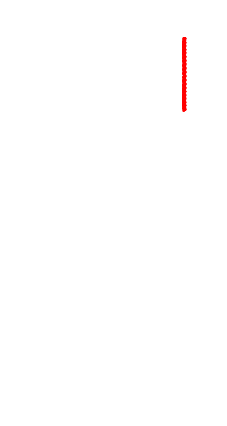

```mathematica
fig5`diPart=With[
{em=Embedding[fig5`disim],
lws=LWSEmbedding[fig5`disim],
flat=FlatEmbedding[fig5`disim],
idx=Index[fig5`disim],
lbl=Function[{txt,coord,bld,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld],
ImageScaled[coord],
{-1,1}]]},
With[
{ymn=Min[flat[[All,3]]],ymx=Max[flat[[All,3]]]},
GraphicsColumn[
Flatten[
{With[
{mn=Min[em[[All,1]]],mx=Max[em[[All,1]]]},
ListPlot[
Map[
{(mx-mn)-(#[[1]]-mn),#[[3]]}&,
em[[#]]&/@idx,
{2}],
BaseStyle->Directive[10,FontFamily->"Arial"],
Axes->None,
FrameLabel->None,
FrameTicks->False,
PlotStyle->{ConeColor[L],ConeColor[S]},
PlotMarkers->{{●,2}},
PlotRange->{{-0.05,mx-mn+0.05},{ymn,ymx+0.005}},
ImageSize->3.0*72,
AspectRatio->0.387]],
With[
{mn=Min[lws[[All,1]]],mx=Max[lws[[All,1]]]},
ListPlot[
Map[
{(mx-mn)-(#[[1]]-mn),#[[3]]}&,
lws],
BaseStyle->Directive[10,FontFamily->"Arial"],
Axes->None,
FrameLabel->None,
FrameTicks->False,
PlotStyle->ConeColor[L],
PlotMarkers->{{●,2}},
PlotRange->{{-0.001,(mx-mn)+0.001},{ymn,ymx+0.005}},
ImageSize->3.0*72,
AspectRatio->0.387]],
With[
{mn=Min[flat[[All,1]]],mx=Max[flat[[All,1]]]},
{ListPlot[
Map[
{(mx-mn)-(#[[1]]-mn),#[[2]]}&,
flat[[All,{1,3}]]],
BaseStyle->Directive[10,FontFamily->"Arial"],
Axes->None,
FrameLabel->None,
FrameTicks->False,
PlotStyle->ConeColor[L],
PlotMarkers->{{●,2}},
PlotRange->{{-0.001,(mx-mn)+0.001},{ymn,ymx+0.005}},
ImageSize->3.0*72,
AspectRatio->0.387],
Show[
{Histogram[
Map[((mx-mn)-(#-mn))&,flat[[All,1]]],
20,
ChartStyle->Gray,
PlotRange->{{-0.001,(mx-mn)+0.001},{0,80}},
Axes->None,
FrameTicks->False,
ImageSize->{3.0,0.2*3.0}*72,
AspectRatio->0.2],
Block[{u,s},
With[
{dist=EstimatedDistribution[
Map[((mx-mn)-(#-mn))&,flat[[All,1]]],
NormalDistribution[u,s],
{{u,(mx-mn)/2},
{s,0.0002}}]},
Plot[
PDF[
dist,
t]/40,
{t,-0.001,(mx-mn)+0.001},
PlotStyle->Thread[{Dashed,ConeColor[L]}],
PlotRange->Full]]]},
ImagePadding->0]}]}],
Spacings->{0,20},
Alignment->{Left,{Center,Center,Center,Top}},
Epilog->{
lbl["(A)",{0,1},Bold,10],
lbl["Dichromat Full Embedding",{0.1,1},Normal,10],
lbl["(B)",{0,0.71},Bold,10],
lbl["Dichromat L Cone Embedding",{0.1,0.71},Normal,10],
lbl["(C)",{0,0.4},Bold,10],
lbl["Dichromat Flattened L Cone Embedding",{0.1,0.4},Normal,10],
lbl["(D)",{0,0.15},Bold,10],
lbl["Dichromat L Cone Histogram and Fits",{0.1,0.15},Normal,10]}]]]
```

#### Tetrachromat

Load Data/Set Params

```mathematica
fig5`tetrasim=First[
Select[
tetrachromatSims,
sim↦And[
Meta[sim,Suppression]=!=0,
LogLM[sim]==0]]];
```

Figure

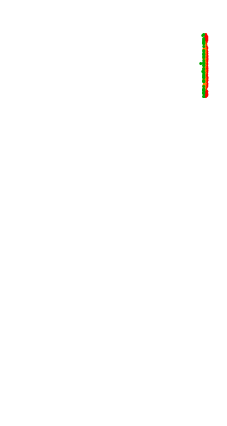

```mathematica
fig5`tetraPart=With[
{sim=fig5`tetrasim,
em=Embedding[fig5`tetrasim],
lws=LWSEmbedding[fig5`tetrasim],
flat=FlatEmbedding[fig5`tetrasim],
idx=Index[fig5`tetrasim],
lwsidx=LWSIndex[fig5`tetrasim],
flatidx=FlatIndex[fig5`tetrasim],
lbl=Function[{txt,coord,bld,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld],
ImageScaled[coord],
{-1,1}]]},
With[
{ymn=Min[em[[All,3]]],ymx=Max[em[[All,3]]]},
GraphicsColumn[
Flatten[
{With[
{mn=Min[em[[All,1]]],mx=Max[em[[All,1]]]},
ListPlot[
Map[
{(mx-mn)-(#[[1]]-mn),#[[3]]}&,
em[[#]]&/@idx,
{2}],
BaseStyle->Directive[10,FontFamily->"Arial"],
Axes->None,
FrameLabel->None,
FrameTicks->False,
PlotStyle->ConeColors[sim][[{1,3,2,4}]],
PlotMarkers->{{●,2}},
PlotRange->{{-0.001,(mx-mn)+0.001},{ymn,ymx+0.002}},
ImageSize->3.0*72,
AspectRatio->0.387]],
With[
{mn=Min[lws[[All,1]]],mx=Max[lws[[All,1]]]},
ListPlot[
Map[
{(mx-mn)-(#[[1]]-mn),#[[3]]}&,
lws[[#]]&/@lwsidx,
{2}],
BaseStyle->Directive[10,FontFamily->"Arial"],
Axes->None,
FrameLabel->None,
FrameTicks->False,
PlotStyle->ConeColors[sim][[{1,3,2}]],
PlotMarkers->{{●,2}},
PlotRange->{{-0.001,(mx-mn)+0.001},{ymn+0.004,ymx+0.006}},
ImageSize->3.0*72,
AspectRatio->0.387]],
With[
{mn=Min[flat[[All,1]]],mx=Max[flat[[All,1]]]},
{ListPlot[
Map[
{(mx-mn)-(#[[1]]-mn),#[[3]]}&,
flat[[#]]&/@flatidx,
{2}],
BaseStyle->Directive[10,FontFamily->"Arial"],
Axes->None,
FrameLabel->None,
FrameTicks->False,
PlotStyle->ConeColors[sim][[{1,3,2}]],
PlotMarkers->{{●,2}},
PlotRange->{{-0.001,(mx-mn)+0.001},{ymn+0.004,ymx+0.006}},
ImageSize->3.0*72,
AspectRatio->0.387],
Show[
{Histogram[
(mx-mn)-(flat[[All,1]]-mn),
35,
ChartStyle->Gray,
PlotRange->{{-0.001,mx-mn+0.001},{0,175}},
Axes->None,
FrameTicks->False,
ImageSize->{3.0,0.2*3.0}*72,
AspectRatio->0.2],
Module[{dist},
ClassifyLWSCones[flat,StepMonitor->((dist=#1)&)];
Plot[
Evaluate[
MapThread[
{w,d}↦w*PDF[d,mx-t]/5,
Transpose[
SortBy[
Transpose[List@@dist],
-#[[2,1]]&]]]],
{t,-0.001,(mx-mn)+0.001},
PlotStyle->Thread[{Dashed,ConeColors[sim][[{2,3,1}]]}],
PlotRange->Full]]},
ImagePadding->0]}]}],
Spacings->{0,20},
Alignment->{Left,{Center,Center,Center,Top}},
Epilog->{
lbl["(E)",{0,1},Bold,10],
lbl["Tetrachromat Full Embedding",{0.1,1},Normal,10],
lbl["(F)",{0,0.71},Bold,10],
lbl["Tetrachromat L, A, and M Cone",{0.1,0.71},Normal,10],
lbl["Embedding",{0.1,0.68},Normal,10],
lbl["(G)",{0,0.4},Bold,10],
lbl["Tetrachromat Flattened L, A, and M",{0.1,0.4},Normal,10],
lbl["Cone Embedding",{0.1,0.37},Normal,10],
lbl["(H)",{0,0.15},Bold,10],
lbl["Tetrachromat L, A, and M Cone Histogram",{0.1,0.15},Normal,10],
lbl["and Fits",{0.1,0.12},Normal,10]}]]]
```

#### Combined

```mathematica
fig5`figure=Graphics[
{Inset[fig5`diPart,ImageScaled[{0,0}],ImageScaled[{0,0}]],
Inset[fig5`tetraPart,ImageScaled[{1,0}],ImageScaled[{1,0}]]},
ImageSize->{6.8,5.5}*72,
ImagePadding->8*72]
```

-Graphics-

#### Export

```mathematica
ExportFigure["figditetra",fig5`figure];
```

### Figure S1: Mosaic Accuracy

#### Load Data/Set Params

```mathematica
figS1`sim=ClojureSim[Samples->2000000,Directory->$ClojureSimDir<>"/standard"];
```

#### Figure

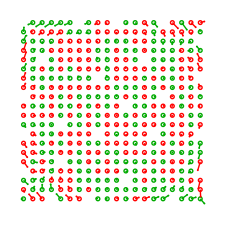

```mathematica
figS1`figure=Block[{xscale,yscale,x0,y0,θ},
With[
{em=Embedding[figS1`sim][[LWS[figS1`sim],{2,3}]],
correct=With[
{simdat=ClojureSimRawData[figS1`sim]},
simdat[[2,LWS[figS1`sim]]]],
types=With[
{simdat=ClojureSimRawData[figS1`sim]},
simdat[[1,LWS[figS1`sim]]]]},
With[
{sol=Quiet[
FindMinimum[
{Total[
MapThread[
EuclideanDistance,
{Map[
#+{x0,y0}&,
Dot[
em,
N[{{xscale*Cos[θ],-yscale*Sin[θ]},
{xscale*Sin[θ],yscale*Cos[θ]}}]]],
correct}]]},
{{xscale,85},{yscale,85},{x0,10.5},{y0,10.5},{θ,60*Pi/180}},
AccuracyGoal->4
][[2]],
{FindMinimum::lstol}]},
With[
{arranged=ReplaceAll[
Map[
#+{x0,y0}&,
Dot[
em,
N[{{xscale*Cos[θ],-yscale*Sin[θ]},
{xscale*Sin[θ],yscale*Cos[θ]}}]]],
sol],
nred=Length[Index[figS1`sim][[1]]]},
Graphics[
MapThread[
{ar,cor,typ}↦{
ConeColors[figS1`sim][[typ+1]],
Circle[Reverse@cor,0.2],
Line[{Reverse@cor,Reverse@ar}],
Disk[Reverse@ar,0.1]},
{arranged,correct,types}],
ImageSize->3.15*72]]]]]
```

#### Export

```mathematica
ExportFigure["figSmosaic",figS1`figure];
```

### Figure S2: Correlation versus Distance

#### Load Data

```mathematica
figS2`sim=ClojureSim[Samples->2000000,Directory->$ClojureSimDir<>"/standard"];
```

#### Make Figure

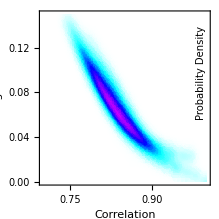

```mathematica
figS2`figure=With[
{R=Correlation[figS2`sim],
D=Outer[EuclideanDistance,Embedding[figS2`sim],Embedding[figS2`sim],1,1]},
With[
{pts=Transpose[
Map[
M↦Select[Flatten[UpperTriangularize[M]],#=!=0&],
{R,D}]]},
SmoothDensityHistogram[
Select[pts,#[[1]]>=0.7&&#[[2]]<=0.15&],
ColorFunctionScaling->False,
ColorFunction->(val↦Blend[{White,Cyan,Blue,Magenta},val/350.0]),
Mesh->True,
Frame->{{True,False},{True,False}},
Axes->None,
PlotRange->{{0.7,1},{0,0.15},Full},
FrameLabel->{{"Embedding Distance",None},{"Correlation",None}},
ImageSize->3.05*72,
AspectRatio->1,
BaseStyle->Directive[10,FontFamily->"Arial"],
Epilog->{
Inset[
ArrayPlot[
Reverse[Table[{k,k},{k,0,350}]],
ColorFunctionScaling->False,
ColorFunction->(val↦Blend[{White,Cyan,Blue,Magenta},val/350.0]),
Axes->None,
Frame->{{False,True},{False,False}},
FrameTicks->{{False,Automatic},{False,False}},
DataRange->{{0,1},{0,350}},
BaseStyle->Directive[10,FontFamily->"Arial"],
ImageSize->0.5*72,
AspectRatio->6],
ImageScaled[{0.8,0.7}],
ImageScaled[{0.5,0.5}]],
Text[
Style["Probability Density",FontSize->10,FontFamily->"Arial"],
{0.99,0.0975},
ImageScaled[{0.5,0.5}],
{0,1}]}]]]
```

#### Export

```mathematica
ExportFigure["figSdist-vs-corr",figS2`figure];
```

### Figure S3: Grid of Embeddings

#### Make Figure

```mathematica
figS3`figure=With[
{sims=fig4`sims1,
dims=Dimensions[fig4`sims1],
text=Function[{txt,pos,bold},
Text[
Style[txt,FontFamily->"Arial",FontSize->10,FontWeight->If[bold,Bold,Normal]],
ImageScaled[pos],
ImageScaled[{0.5,0.5}]]],
textRot=Function[{txt,pos,bold},
Text[
Style[txt,FontFamily->"Arial",FontSize->10,FontWeight->If[bold,Bold,Normal]],
ImageScaled[pos],
ImageScaled[{0.5,0.5}],
{0,1}]]},
Block[{x,y,z},
Graphics[
Join[
MapIndexed[
{sim,idx}↦Inset[
ListPointPlot3D[
LWSEmbedding[sim][[#]]&/@LWSIndex[sim],
PlotStyle->Map[{#,PointSize[0.02]}&,ConeColors[sim]],
BoxRatios->{1,1,1},
Ticks->None,
AxesLabel->{z,y,x},
ImageSize->0.7*72,
AspectRatio->1,
BaseStyle->Directive[10,FontFamily->"Times"]],
ImageScaled[{0.07+0.93*(idx[[2]]-1)/dims[[2]],0.075+0.925*(idx[[1]]-1)/dims[[1]]}],
ImageScaled[{0,0}]],
sims,
{2}],
{textRot["M cone λ_max",{0.02,0.53},False],
text["L:M ratio",{0.53,0.02},False],
MapThread[
text[#1,{0.1+0.925*(#2-1)/9,0.05},True]&,
{{"1:16","1:8","1:4","1:2","1:1","2:1","4:1","8:1","16:1"},
Range[9]}],
MapThread[
textRot[#1,{0.05,0.14+0.925*(#2-1)/6},True]&,
{{"530","535","540","545","550","555"},
Range[6]}]
}],
ImageSize->{7,5.5}*72,
ImagePadding->10000]]]
```

-Graphics-

#### Export

```mathematica
ExportFigure["figSemgrid",figS3`figure];
```

### Figure S4: Individual Simulation Results

#### Percentage classified correctly if k=2

```mathematica
figS4`eachsimcorrect=Map[
AccuracyPlot,
{fig4`dat1,fig4`dat2,fig4`dat3}]
```

{-Graphics-,-Graphics-,-Graphics-}

#### Number of classes found in each simulation

```mathematica
figS4`eachsimclasses=Map[
ClustersPlot[#,Range->{1,3}]&,
{fig4`k1,fig4`k2,fig4`k3}]
```

{-Graphics-,-Graphics-,-Graphics-}

#### Combined

```mathematica
figS4`eachsim=Module[
{lbl=Function[{txt,coord,bld,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld],
ImageScaled[coord],
ImageScaled[{0,0}]]]},
Graphics[
Join[
MapThread[
Inset[#1,ImageScaled[{0,#2}],ImageScaled[{0,0}]]&,
{figS4`eachsimcorrect,
{0,1/3,2/3}}],
MapThread[
Inset[#1,ImageScaled[{0.5,#2}],ImageScaled[{0,0}]]&,
{figS4`eachsimclasses,
{0,1/3,2/3}}]],
ImagePadding->6.5*72,
ImageSize->{6.5,6.5}*72,
Epilog->{
lbl["(A)",{0,0.97},Bold,10],
lbl["(B)",{0,0.65},Bold,10],
lbl["(C)",{0,0.315},Bold,10],
lbl["Simulation 1",{0.05,0.97},Normal,10],
lbl["Simulation 2",{0.05,0.65},Normal,10],
lbl["Simulation 3",{0.05,0.315},Normal,10],

lbl["Fraction Correctly Classified",{0.09,0.95},Normal,10],
lbl["Number of Cone Classses Found",{0.57,0.95},Normal,10],
lbl["Fraction Correctly Classified",{0.09,0.62},Normal,10],
lbl["Number of Cone Classses Found",{0.57,0.62},Normal,10],
lbl["Fraction Correctly Classified",{0.09,0.285},Normal,10],
lbl["Number of Cone Classses Found",{0.57,0.285},Normal,10],
Inset[
Graphics[{White,Rectangle[{0,0},{3,40}]}],
ImageScaled[{0.52,0}],
ImageScaled[{0.5,0}]],
Inset[
Graphics[{White,Rectangle[{0,0},{3,40}]}],
ImageScaled[{0.52,0.92}],
ImageScaled[{0.5,1}]]}]]
```

-Graphics-

#### Export

```mathematica
ExportFigure["figSeachsim",figS4`eachsim];
```

### Figure S5: Performance of 10 x 10 and 15 x 15

#### Load Data

```mathematica
figS5`sims10=Map[
SortBy[#,Meta[#,Ls]&]&,
SplitBy[
SortBy[
Select[
standardSims,
sim↦And[
Meta[sim,Run]==0,
Meta[sim,Suppression]==0,
Meta[sim,RetinaSize]==10,
Meta[sim,Samples]==2000000]],
Meta[#,MΛMax]&],
Meta[#,MΛMax]&]];
figS5`sims15=Map[
SortBy[#,Meta[#,Ls]&]&,
SplitBy[
SortBy[
Select[
standardSims,
sim↦And[
Meta[sim,Run]==0,
Meta[sim,Suppression]==0,
Meta[sim,RetinaSize]==15,
Meta[sim,Samples]==2000000]],
Meta[#,MΛMax]&],
Meta[#,MΛMax]&]];
```

#### 10 x 10 Accuracy

```mathematica
figS5`dat10=Map[
sim↦ClassificationScore[sim,ClassCount->2],
figS5`sims10,
{2}];
```

```mathematica
figS5`partA=AccuracyPlot[figS5`dat10]
```

-Graphics-

#### 10 x 10 where k=2

```mathematica
figS5`k10=Map[
sim↦ClassesFound[sim],
figS5`sims10,
{2}];
```

```mathematica
figS5`partC=ClustersPlot[figS5`k10,Range->{1,3}]
```

-Graphics-

#### 15 x 15 Accuracy

```mathematica
figS5`dat15=Map[
sim↦ClassificationScore[sim,ClassCount->2],
figS5`sims15,
{2}];
```

```mathematica
figS5`partB=AccuracyPlot[figS5`dat15]
```

-Graphics-

#### 15 x 15 where k=2

```mathematica
figS5`k15=Map[
sim↦ClassesFound[sim],
figS5`sims15,
{2}];
```

```mathematica
figS5`partD=ClustersPlot[figS5`k15,Range->{1,3}]
```

-Graphics-

#### Combined

```mathematica
figS5`figure=With[
{lbl=Function[{txt,coord,bld,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld],
ImageScaled[coord],
ImageScaled[{0,0}]]],
A=Graphics[
{Inset[figS5`partA,ImageScaled[{0,0}],ImageScaled[{0,0}]]},
ImageSize->{2.75,2.05}*72,
ImagePadding->4*72],
C=Graphics[
{Inset[figS5`partC,ImageScaled[{0,0}],ImageScaled[{0,0}]]},
ImageSize->{2.75,2.05}*72,
ImagePadding->4*72]},
Graphics[
{Inset[figS5`partB,ImageScaled[{0.6025,0.75}],ImageScaled[{0.5,0.5}]],
Inset[figS5`partD,ImageScaled[{0.6025,0.25}],ImageScaled[{0.5,0.5}]],
Inset[C,ImageScaled[{0.25,0.25}],ImageScaled[{0.5,0.5}]],
Inset[A,ImageScaled[{0.25,0.75}],ImageScaled[{0.5,0.5}]]},
ImageSize->{6.1,4.35}*72,
ImagePadding->6.1*72,
Epilog->List[
lbl["(A)",{0.05,0.965},Bold,10],
lbl["Fraction Correctly Classified",{0.1,0.965},Normal,10],
lbl["(B)",{0.05,0.465},Bold,10],
lbl["Number of Cone Classes Found",{0.1,0.465},Normal,10],
lbl["10×10",{0.24,0.935},Normal,10],
lbl["15×15",{0.555,0.935},Normal,10],
lbl["10×10",{0.24,0.435},Normal,10],
lbl["15×15",{0.555,0.435},Normal,10]]]]
```

-Graphics-

#### Export

```mathematica
ExportFigure["figSaccuracy-10-15",figS5`figure];
```

### Figure S6: Samples Versus Accuracy

#### Prep Data

```mathematica
figS6`sims=Map[
SortBy[#,Meta[#,Samples]&]&,
SplitBy[
SortBy[
Select[
samplesSims,
sim↦And[
Meta[sim,Suppression]=!=0,
Meta[sim,RetinaSize]==20,
Meta[sim,Samples]≤2000000]],
{Meta[#,MΛMax],Meta[#,Ls]}&],
{Meta[#,MΛMax],Meta[#,Ls]}&]];
```

#### Plot

```mathematica
figS6`figure=With[
{sims=figS6`sims,
colors={Darker@Cyan,Black,Darker@Magenta}},
With[
{simsGrouped=Map[
ids↦SortBy[ids,id↦Meta[sims[[id,1]],Ls]],
GatherBy[
Range[Length@sims],
id↦Meta[sims[[id,1]],MΛMax]]]},
Graphics[
Join[
Map[
ids↦With[
{dat=Map[
id↦Map[
(*group↦{
{group[[1,1]],Mean[group[[All,2]]]},
ErrorBar[Sqrt[Variance[group[[All,2]]]/Length[group]]]},*)
group↦{group[[1,1]],Mean[group[[All,2]]]},
GatherBy[
Map[
{Meta[#,Samples],ClassificationScore[#,ClassCount->2]}&,
sims[[id]]],
First]],
ids],
mlm=Meta[sims[[ids[[1]],1]],MΛMax]},
Inset[
ListPlot[
N@dat,
Joined->True,
PlotRange->{{0,2050000},{0.5,1.02}},
ImageSize->3*72,
AspectRatio->0.4,
BaseStyle->Directive[10,FontFamily->"Arial"],
Axes->None,
Frame->{{True,False},{True,False}},
FrameTicks->{{Automatic,None},{{{0,0},{500000,5},{1000000,10},{1500000,15},{2000000,20}},None}},
FrameLabel->None,
PlotMarkers->{▲,◆,●},
PlotStyle->Thread[{colors,{Dashing[{}],Dashing[{}],Dashing[{}]}}]],
ImageScaled[{0.07,0.05+Replace[mlm,{530->0.01,540->0.33,550->0.64}]}],
ImageScaled[{0,0}]]],
simsGrouped],
{Text[
Style["Fraction Correctly Classified",FontSize->10,FontFamily->"Arial"],
ImageScaled[{0.02,0.55}],
ImageScaled[{0.5,0.5}],
{0,1}],
Text[
Style["Number of Simulated Images (×10^5)",FontSize->10,FontFamily->"Arial"],
ImageScaled[{0.55,0}],
ImageScaled[{0.5,0}]],
Text[
Style["M λ-max = 530 nm",FontSize->10,FontFamily->"Arial"],
ImageScaled[{0.3,0.36}],
ImageScaled[{0.5,0.5}]],
Text[
Style["M λ-max = 540 nm",FontSize->10,FontFamily->"Arial"],
ImageScaled[{0.3,0.68}],
ImageScaled[{0.5,0.5}]],
Text[
Style["M λ-max = 550 nm",FontSize->10,FontFamily->"Arial"],
ImageScaled[{0.3,0.99}],
ImageScaled[{0.5,0.5}]],
Inset[
Graphics[
{{colors[[1]],Dashing[{}],Line[{{-1,1},{1,1}}],
Text["▲",{0,1},ImageScaled[{0.5,0.5}]],
Text["log_2(L:M) = -2",{1.25,1},ImageScaled[{0,0.5}]]},
{colors[[2]],Dashing[{}],Line[{{-1,0},{1,0}}],
Text["◆",{0,0},ImageScaled[{0.5,0.5}]],
Text["log_2(L:M) = 0",{1.25,0},ImageScaled[{0,0.5}]]},
{colors[[3]],Dashing[{}],Line[{{-1,-1},{1,-1}}],
Text["●",{0,-1},ImageScaled[{0.5,0.5}]],
Text["log_2(L:M) = 2",{1.25,-1},ImageScaled[{0,0.5}]]}},
ImageSize->1.35*72,
AspectRatio->1],
ImageScaled[{0.775,0.2}],
ImageScaled[{0.5,0.5}]]}],
ImageSize->{3.25,4.75}*72,
ImagePadding->2000]]]
```

-Graphics-

#### Export

```mathematica
ExportFigure["figSsamples",figS6`figure];
```

### Figure S7: Performance w/o Surround

#### Load Data

```mathematica
figS7`sims=Map[
SortBy[#,Meta[#,Ls]&]&,
SplitBy[
SortBy[
Select[
standardSims,
sim↦And[
Meta[sim,Run]===0,
Meta[sim,Suppression]===0,
Meta[sim,RetinaSize]===20,
Meta[sim,Samples]===2000000]],
Meta[#,MΛMax]&],
Meta[#,MΛMax]&]];
```

#### Accuracy

```mathematica
figS7`dat=Map[
sim↦ClassificationScore[sim,ClassCount->2],
figS7`sims,
{2}];
```

```mathematica
figS7`partA=AccuracyPlot[figS7`dat]
```

-Graphics-

#### Where k=2

```mathematica
figS7`types=Map[
ClassesFound,
figS7`sims,
{2}];
```

```mathematica
figS7`partB=ClustersPlot[figS7`types,Range->{1,3}]
```

-Graphics-

#### Combined

```mathematica
figS7`figure=With[
{lbl=Function[{txt,coord,bld,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld],
ImageScaled[coord],
ImageScaled[{0,0}]]]},
Graphics[
{Inset[figS7`partA,ImageScaled[{0.5,0.75}],ImageScaled[{0.5,0.5}]],
Inset[figS7`partB,ImageScaled[{0.5,0.25}],ImageScaled[{0.5,0.5}]]},
ImageSize->{3.25,4.25}*72,
ImagePadding->5*72,
Epilog->List[
lbl["(A)",{0.05,0.95},Bold,10],
lbl["Fraction Correctly Classified",{0.15,0.95},Normal,10],
lbl["(B)",{0.05,0.45},Bold,10],
lbl["Number of Cone Classes Found",{0.15,0.45},Normal,10]]]]
```

-Graphics-

#### Export

```mathematica
ExportFigure["figSaccuracy-nosurround",figS7`figure];
```

### Figure S8: Performance with cone-specific surrounds

#### Load Data

```mathematica
figS8`sims=Map[
SortBy[#,Meta[#,Ls]&]&,
SplitBy[
SortBy[
Select[
opponentSims,
sim↦And[
Meta[sim,Suppression]=!=0,
Meta[sim,Samples]==2000000]],
Meta[#,MΛMax]&],
Meta[#,MΛMax]&]];
```

#### Accuracy

```mathematica
figS8`dat=Map[
sim↦ClassificationScore[sim,ClassCount->2],
figS8`sims,
{2}];
```

```mathematica
figS8`partA=AccuracyPlot[figS8`dat]
```

-Graphics-

#### Where k=2

```mathematica
figS8`k=Map[
ClassesFound,
figS8`sims,
{2}];
```

```mathematica
figS8`partB=ClustersPlot[figS8`k,Range->{1,3}]
```

-Graphics-

#### Combined

```mathematica
figS8`figure=With[
{lbl=Function[{txt,coord,bld,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld],
ImageScaled[coord],
ImageScaled[{0,0}]]]},
Graphics[
{Inset[figS8`partA,ImageScaled[{0.5,0.75}],ImageScaled[{0.5,0.5}]],
Inset[figS8`partB,ImageScaled[{0.5,0.25}],ImageScaled[{0.5,0.5}]]},
ImageSize->{3.25,4.25}*72,
ImagePadding->5*72,
Epilog->List[
lbl["(A)",{0.05,0.95},Bold,10],
lbl["Fraction Correctly Classified",{0.15,0.95},Normal,10],
lbl["(B)",{0.05,0.45},Bold,10],
lbl["Number of Cone Classes Found",{0.15,0.45},Normal,10]]]]
```

-Graphics-

#### Export

```mathematica
ExportFigure["figSaccuracy-opponent",figS8`figure];
```

### Figure S9: Performance with Tritanopes

#### Load Data

```mathematica
figS9`sims=Map[
SortBy[#,Meta[#,Ls]&]&,
SplitBy[
SortBy[
Select[
tritanopeSims,
sim↦And[
Meta[sim,Suppression]=!=0,
Meta[sim,RetinaSize]==20,
Meta[sim,Samples]==4500000]],
Meta[#,MΛMax]&],
Meta[#,MΛMax]&]];
```

#### Accuracy

```mathematica
figS9`dat=Map[
sim↦ClassificationScore[sim,ClassCount->2],
figS9`sims,
{2}];
```

```mathematica
figS9`partA=AccuracyPlot[figS9`dat,Simulations->figS9`sims]
```

-Graphics-

#### Where k=2

```mathematica
figS9`k=Map[
ClassesFound,
figS9`sims,
{2}];
```

```mathematica
figS9`partB=ClustersPlot[figS9`k,Simulations->figS9`sims,Range->{1,3}]
```

-Graphics-

#### Combined

```mathematica
figS9`figure=With[
{lbl=Function[{txt,coord,bld,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld],
ImageScaled[coord],
ImageScaled[{0,0}]]]},
Graphics[
{Inset[figS9`partA,ImageScaled[{0.5,0.75}],ImageScaled[{0.5,0.5}]],
Inset[figS9`partB,ImageScaled[{0.5,0.25}],ImageScaled[{0.5,0.5}]]},
ImageSize->{3.25,4.25}*72,
ImagePadding->5*72,
Epilog->List[
lbl["(A)",{0.05,0.95},Bold,10],
lbl["Fraction Correctly Classified",{0.15,0.95},Normal,10],
lbl["(B)",{0.05,0.45},Bold,10],
lbl["Number of Cone Classes Found",{0.15,0.45},Normal,10]]]]
```

-Graphics-

#### Export

```mathematica
ExportFigure["figSaccuracy-lmonly",figS9`figure];
```

### Figure S10: Performance w/o Man-made Images

#### Load Data

```mathematica
figS10`sims=Map[
SortBy[#,Meta[#,Ls]&]&,
SplitBy[
SortBy[
Select[
naturalSims,
sim↦And[
Meta[sim,Run]==1,
Meta[sim,Suppression]=!=0,
Meta[sim,RetinaSize]==20]],
Meta[#,MΛMax]&],
Meta[#,MΛMax]&]];
```

#### Accuracy

```mathematica
figS10`dat=Map[
sim↦ClassificationScore[sim,ClassCount->2],
figS10`sims,
{2}];
```

```mathematica
figS10`partA=AccuracyPlot[figS10`dat]
```

-Graphics-

#### Where k=2

```mathematica
figS10`k=Map[
sim↦ClassesFound[sim],
figS10`sims,
{2}];
```

```mathematica
figS10`partB=ClustersPlot[figS10`k,Range->{1,3}]
```

-Graphics-

#### Combined

```mathematica
figS10`figure=With[
{lbl=Function[{txt,coord,bld,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld],
ImageScaled[coord],
ImageScaled[{0,0}]]]},
Graphics[
{Inset[figS10`partA,ImageScaled[{0.5,0.75}],ImageScaled[{0.5,0.5}]],
Inset[figS10`partB,ImageScaled[{0.5,0.25}],ImageScaled[{0.5,0.5}]]},
ImageSize->{3.25,4.25}*72,
ImagePadding->5*72,
Epilog->List[
lbl["(A)",{0.05,0.95},Bold,10],
lbl["Fraction Correctly Classified",{0.15,0.95},Normal,10],
lbl["(B)",{0.05,0.45},Bold,10],
lbl["Number of Cone Classes Found",{0.15,0.45},Normal,10]]]]
```

-Graphics-

#### Export

```mathematica
ExportFigure["figSaccuracy-nomanmade",figS10`figure];
```

### Figure S11: Performance with noise

#### Load Data

```mathematica
figS11`sims1=Map[
SortBy[#,Meta[#,Ls]&]&,
SplitBy[
SortBy[
Select[
noise1Sims,
sim↦And[
Meta[sim,Suppression]=!=0,
Meta[sim,RetinaSize]==20,
Meta[sim,Samples]==2000000]],
Meta[#,MΛMax]&],
Meta[#,MΛMax]&]];
```

```mathematica
figS11`sims5=Map[
SortBy[#,Meta[#,Ls]&]&,
SplitBy[
SortBy[
Select[
noise5Sims,
sim↦And[
Meta[sim,Suppression]=!=0,
Meta[sim,RetinaSize]==20,
Meta[sim,Samples]==2000000]],
Meta[#,MΛMax]&],
Meta[#,MΛMax]&]];
```

#### Figure S11A: Accuracy

```mathematica
figS11`dat1=Map[
sim↦ClassificationScore[sim,ClassCount->2],
figS11`sims1,
{2}];
```

```mathematica
figS11`dat5=Map[
sim↦ClassificationScore[sim,ClassCount->2],
figS11`sims5,
{2}];
```

```mathematica
figS11`partA1=First[AccuracyPlot[figS11`dat1,SeparateLegend->True]]
```

-Graphics-

```mathematica
{figS11`partA5,figS11`legendA}=AccuracyPlot[figS11`dat5,SeparateLegend->True]
```

{-Graphics-,-Graphics-}

#### Figure S11B: Where k=2

```mathematica
figS11`k1=Map[
ClassesFound,
figS11`sims1,
{2}];
```

```mathematica
figS11`k5=Map[
ClassesFound,
figS11`sims5,
{2}];
```

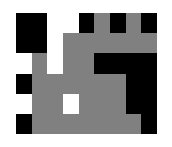

```mathematica
figS11`partB1=First[ClustersPlot[figS11`k1,Range->{1,3},SeparateLegend->True]]
```

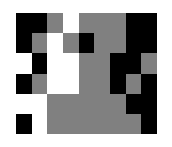
{-Graphics-,-Graphics-}

```mathematica
{figS11`partB5,figS11`legendB}=ClustersPlot[figS11`k5,Range->{1,3},SeparateLegend->True]
```

#### Combined

```mathematica
figS11`figure=With[
{lbl=Function[{txt,coord,bld,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld],
ImageScaled[coord],
ImageScaled[{0,0}]]]},
Graphics[
{Inset[figS11`partA5,ImageScaled[{0.38,0.7}],ImageScaled[{0,0.5}]],Inset[figS11`partA1,ImageScaled[{0,0.7}],ImageScaled[{0,0.5}]],
Inset[figS11`legendA,ImageScaled[{0.9,0.75}],ImageScaled[{0,0.5}]],
Inset[figS11`partB5,ImageScaled[{0.38,0.2}],ImageScaled[{0,0.5}]],Inset[figS11`partB1,ImageScaled[{0,0.2}],ImageScaled[{0,0.5}]],
Inset[figS11`legendB,ImageScaled[{0.9,0.25}],ImageScaled[{0,0.5}]]},
ImageSize->{5,4.35}*72,
ImagePadding->5*72,
Epilog->List[
lbl["(A)",{0.05,0.95},Bold,10],
lbl["Fraction Correctly Classified",{0.15,0.95},Normal,10],
lbl["(B)",{0.05,0.45},Bold,10],
lbl["Number of Cone Classes Found",{0.15,0.45},Normal,10],
lbl["1% Noise",{0.225,0.905},Normal,10],
lbl["1% Noise",{0.225,0.405},Normal,10],
lbl["5% Noise",{0.6,0.905},Normal,10],
lbl["5% Noise",{0.6,0.405},Normal,10]
]]]
```

-Graphics-

#### Export

```mathematica
ExportFigure["figSaccuracy-noise",figS11`figure];
```

### Figure S12: Performance with blur

#### Load Data

```mathematica
figS12`sims=Map[
SortBy[#,Meta[#,Ls]&]&,
SplitBy[
SortBy[
Select[
blurSims,
sim↦And[
Meta[sim,Suppression]=!=0,
Meta[sim,RetinaSize]==20]],
Meta[#,MΛMax]&],
Meta[#,MΛMax]&]];
```

#### Accuracy

```mathematica
figS12`dat=Map[
sim↦ClassificationScore[sim,ClassCount->2],
figS12`sims,
{2}];
```

```mathematica
figS12`partA=AccuracyPlot[figS12`dat]
```

-Graphics-

#### Where k=2

```mathematica
figS12`k=Map[
sim↦ClassesFound[sim],
figS12`sims,
{2}];
```

```mathematica
figS12`partB=ClustersPlot[figS12`k,Range->{1,3}]
```

-Graphics-

#### Combined

```mathematica
figS12`figure=With[
{lbl=Function[{txt,coord,bld,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld],
ImageScaled[coord],
ImageScaled[{0,0}]]]},
Graphics[
{Inset[figS12`partA,ImageScaled[{0.5,0.75}],ImageScaled[{0.5,0.5}]],
Inset[figS12`partB,ImageScaled[{0.5,0.25}],ImageScaled[{0.5,0.5}]]},
ImageSize->{3.25,4.25}*72,
ImagePadding->5*72,
Epilog->List[
lbl["(A)",{0.05,0.95},Bold,10],
lbl["Fraction Correctly Classified",{0.15,0.95},Normal,10],
lbl["(B)",{0.05,0.45},Bold,10],
lbl["Number of Cone Classes Found",{0.15,0.45},Normal,10]]]]
```

-Graphics-

#### Export

```mathematica
ExportFigure["figSaccuracy-blur",figS12`figure];
```

## Other Analyses

### Nonhuman Tetrachromats: Performance with spectrally-spaced M cones

#### Load Data

```mathematica
nonhumanAnalysis`sims=Map[
SortBy[#,Meta[#,Ls]&]&,
SplitBy[
SortBy[
Select[
nonhumanSims,
sim↦And[
Meta[sim,Suppression]=!=0,
Meta[sim,RetinaSize]==20,
Meta[sim,Samples]==2000000]],
Meta[#,MΛMax]&],
Meta[#,MΛMax]&]];
```

#### Accuracy

```mathematica
nonhumanAnalysis`dat=Map[
sim↦ClassificationScore[sim],
nonhumanAnalysis`sims,
{2}];
```

```mathematica
AccuracyPlot[nonhumanAnalysis`dat]
```

-Graphics-

#### Figure S8B: Where k=2

```mathematica
nonhumanAnalysis`k=Map[
ClassesFound,
nonhumanAnalysis`sims,
{2}];
```

```mathematica
ClustersPlot[nonhumanAnalysis`k,Range->{1,3}]
```

-Graphics-

### Performance of tetrachromatic mosaic by cone type

This produces a list of rules mapping cone type to the fraction correcrtly classified.

```mathematica
Reap[
MapThread[
{found,true}↦If[found==true,Sow[1,true],Sow[0,true]],
{ConeClasses[fig5`tetrasim],
TrueClasses[fig5`tetrasim]}],
{1,2,3},
{class,scores}↦(Replace[class,{1->L,2->M,3->A}]->N[Total[scores]/Length[scores]])
][[2,All,1]]
```

{L→1.,M→1.,A→0.84127}

### L-M Selectivity

This measure comes from Wachtler, Doi, Lee, Sejnowski (2007) J Vis. 7(8):6. It describes a measure for estimating the L versus M cone selectivity of a particular unit, e.g., a principal component or dimension of the MDS.

#### Setup Function

This function yields three functions: (lgen, mgen, totalfn}. All three should be given a single unit (e.g., the real values of a principal component or a dimension of the MDS solution). The lgen and mgen functions yield functions: l[x,y] and m[x,y] from the Wachtler paper, pages 4 and 5. The totalfn yields the denominator of the cLM index (page 5 of the Wachtler paper).

```mathematica
ClearAll[LMSelectivity];
LMSelectivity[sim_]:=With[
{G=Function[{x,x0},(Exp[-0.5*Total[(x-x0)^2]]/N[2*Pi])],
X=Flatten[MapIndexed[#2&,Retina[sim]ᵀ,{2}],1],
ms=Index[sim][[2]],
ls=Index[sim][[1]]},
{Function[{zs},
Function[{x,y},Dot[zs[[ls]],Map[G[#,{x,y}]&,X[[ls]]]]]],
Function[{zs},
Function[{x,y},Dot[zs[[ms]],Map[G[#,{x,y}]&,X[[ms]]]]]],
Function[{zs},
Total[Abs[zs[[ls]]]]+Total[Abs[zs[[ms]]]]]}];
```

#### Calculate Data

Calculate the L-M selectivity of each of the principal components of the 500,000 images simulation that is most similar to the Wachtler et al simulations.

```mathematica
lmsel500000=With[
{wachtlerLikeSim=First[
Select[
basicSims,
sim↦And[Meta[sim,Ls]==63,Meta[sim,MΛMax]==530]]]},
With[
{fns=LMSelectivity[wachtlerLikeSim],
pca=pca},
ParallelTable[
Quiet[
With[
{l=fns[[1]][pca[[k]]],
m=fns[[2]][pca[[k]]],
total=fns[[3]][pca[[k]]]},
Divide[
NIntegrate[
Abs[l[x,y]-m[x,y]],
{x,-3,24},
{y,-3,24}],
total]]],
{k,1,Length[pca]}]]];
```

```mathematica
lmsel500000sh=With[
{wachtlerLikeSim=First[
Select[
basicSims,
sim↦And[Meta[sim,Ls]==63,Meta[sim,MΛMax]==530]]]},
With[
{simSh=With[
{id=Unique["simSh"]},
id/:Retina[id]=Partition[RandomSample[Flatten[Retina[wachtlerLikeSim]],400],20];
id/:Index[id]=Table[
Flatten[Position[Flatten[Retina[id]],k,{1},Heads->False]],
{k,{1,2}}];
id]},
With[
{fns=LMSelectivity[simSh],
pca=pca},
Table[
With[
{l=fns[[1]][pca[[k]]],
m=fns[[2]][pca[[k]]],
total=fns[[3]][pca[[k]]]},
Divide[
NIntegrate[
Abs[l[x,y]-m[x,y]],
{x,-3,24},
{y,-3,24}],
total]],
{k,1,Length[pca]}]]]];
```

Also run the same thing but with a full 2,000,000 images.

```mathematica
lmsel2000000=With[
{sim=fig4`sims2[[1,6]]},
With[
{V=Eigensystem[Correlation[sim]][[2,2;;All]]},
With[
{fns=LMSelectivity[sim]},
Table[
With[
{l=fns[[1]][V[[k]]],
m=fns[[2]][V[[k]]],
total=fns[[3]][V[[k]]]},
Divide[
NIntegrate[
Abs[l[x,y]-m[x,y]],
{x,-3,24},
{y,-3,24}],
total]],
{k,1,Length[V]}]]]];
```

```mathematica
lmsel2000000sh=With[
{sim=fig4`sims2[[1,6]]},
With[
{simSh=With[
{id=Unique["simSh"]},
id/:Retina[id]=Partition[RandomSample[Flatten[Retina[sim]],400],20];
id/:Index[id]=Table[
Flatten[Position[Flatten[Retina[id]],k,{1},Heads->False]],
{k,{1,2}}];
id]},
With[
{fns=LMSelectivity[simSh],
pca=Eigensystem[Correlation[sim]][[2,2;;All]]},
Table[
With[
{l=fns[[1]][pca[[k]]],
m=fns[[2]][pca[[k]]],
total=fns[[3]][pca[[k]]]},
Divide[
NIntegrate[
Abs[l[x,y]-m[x,y]],
{x,-3,24},
{y,-3,24}],
total]],
{k,1,Length[pca]}]]]];
```

#### Image

```mathematica
Graphics[
{Inset[
Histogram[
lmsel500000,
BaseStyle->Directive[10,FontFamily->"Arial"],
ChartStyle->Gray,
ImageSize->3.25*72,
AspectRatio->0.4,
PlotRange->{{0,1},{0,90}},
Axes->None,
Frame->{{True,False},{True,False}},
FrameLabel->{{"Frequency",None},{"L-M selectivity index",None}}],
ImageScaled[{0,0.5}],
ImageScaled[{0,0}]],
Inset[
Histogram[
lmsel2000000,
BaseStyle->Directive[10,FontFamily->"Arial"],
ChartStyle->Gray,
ImageSize->3.25*72,
AspectRatio->0.4,
PlotRange->{{0,1},{0,90}},
Axes->None,
Frame->{{True,False},{True,False}},
FrameLabel->{{"Frequency",None},{"L-M selectivity index",None}}],
ImageScaled[{0,0}],
ImageScaled[{0,0}]],
Text[
Style["500,000 samples",FontSize->10,FontFamily->"Arial"],
ImageScaled[{0.75,0.75}],
ImageScaled[{0.5,0.5}]],
Text[
Style["2,000,000 samples",FontSize->10,FontFamily->"Arial"],
ImageScaled[{0.75,0.25}],
ImageScaled[{0.5,0.5}]]},
ImageSize->{3.25,3.25}*72,
ImagePadding->2000]
```

-Graphics-

```mathematica
Graphics[
{Inset[
Histogram[
lmsel500000sh,
BaseStyle->Directive[10,FontFamily->"Arial"],
ChartStyle->Gray,
ImageSize->3.25*72,
AspectRatio->0.4,
PlotRange->{{0,1},{0,90}},
Axes->None,
Frame->{{True,False},{True,False}},
FrameLabel->{{"Frequency",None},{"L-M selectivity index",None}}],
ImageScaled[{0,0.5}],
ImageScaled[{0,0}]],
Inset[
Histogram[
lmsel500000sh,
BaseStyle->Directive[10,FontFamily->"Arial"],
ChartStyle->Gray,
ImageSize->3.25*72,
AspectRatio->0.4,
PlotRange->{{0,1},{0,90}},
Axes->None,
Frame->{{True,False},{True,False}},
FrameLabel->{{"Frequency",None},{"L-M selectivity index",None}}],
ImageScaled[{0,0}],
ImageScaled[{0,0}]],
Text[
Style["500,000 samples\n(shuffled)",FontSize->10,FontFamily->"Arial"],
ImageScaled[{0.75,0.75}],
ImageScaled[{0.5,0.5}]],
Text[
Style["2,000,000 samples\n(shuffled)",FontSize->10,FontFamily->"Arial"],
ImageScaled[{0.75,0.25}],
ImageScaled[{0.5,0.5}]]},
ImageSize->{3.25,3.25}*72,
ImagePadding->2000]
```

-Graphics-

## Export 3D Rotating Embeddings

#### Function for exporting 3D sims in bulk

```mathematica
ExportRotatingImages[sims_List,tag_String,type:(Full|LWS|Flat)]:=Map[
sim↦With[
{flnm=StringJoin[
$FiguresDir,"/3D/",tag<>".",
Switch[type,Full,"full",LWS,"zoom",Flat,"flat"],
"_Mlmax=",ToString[Meta[sim,MΛMax]],
"_logLM=",ToString[LogLM[sim]],
".gif"]},
If[!FileExistsQ[flnm],
Export[
flnm,
Rotating3DEmbedding[sim,type],
"GIF",
ImageResolution->300,
"DisplayDuration"->0.15]]],
sims,
{2}];
```

#### Export all sets of simulations

```mathematica
MapThread[
{simSet,tag}↦(
ExportRotatingImages[simSet,tag,Full];
ExportRotatingImages[simSet,tag,LWS];
ExportRotatingImages[simSet,tag,Flat]),
Transpose[
{{fig4`sims1,"fig4sims1"},
{fig4`sims2,"fig4sims2"},
{fig4`sims3,"fig4sims3"},
{figS5`sims10,"figS5retina10x10"},
{figS5`sims15,"figS5retina15x15"},
{figS7`sims,"figS8nosurround"},
{figS8`sims,"figS12opponent"},
{figS10`sims,"figS9natural"},
{figS11`sims,"figS11noise"},
{figS12`sims,"figS10blur"}}]]
```